# Phospholipid Model

```mathematica
doExport=True
FASmodelYear="2020" (* Choose 2020 or 2022 *)
malCoaConc=250 (* In micromolar *)
ACPconc=48 (* In micromolar *)
nA=6.02214*10^23;
nPLpCell=22*10^6;
Vcell=3*10^-15;(* L/cell *)

correctionFactorFluxLPS=1
optParams={
alpha->999999999,
beta->731.439, (*731.4394849853176 is best*)
gamma->999999999,
nu->1}; (* 999 999 999 means the term does not contribute *)

RatesAcACPs={ (* Unbound *)
kcat61 y100,(* C4-ACP *)
kcat62 y115,(* C6-ACP *)
kcat63 y130,(* C8-ACP *)
kcat64 y145,(* C10-ACP *)
kcat65 y160,(* C12-ACP *)
kcat66 y175,(* C14-ACP *)
kcat67 y190,(* C16-ACP *)
kcat68 y205, (* C18-ACP *)
kcat69 y220, (* C20-ACP *)
kcat65 y229,(* C12u-ACP *)
kcat66 y244,(* C14u-ACP *)
kcat67 y259,(* C16u-ACP *)
kcat68 y274,(* C18u-ACP *)
kcat69 y289 (* C20u-ACP *)
};
```

True

2020

250

48

1

## Import the Model

Import parameters

```mathematica
(* FAS *)
kinParamsFAS=Import[FileNameJoin[{NotebookDirectory[],"data/FAS",FASmodelYear<>"_fox_kinetic_params.csv"}]];
kinParamsFAS=Symbol[StringReplace[ToString[#[[1]]],"_"->""]]->#[[2]]&/@kinParamsFAS;
enzymeConcsFAS=Import[FileNameJoin[{NotebookDirectory[],"data/FAS","FAS_enzyme_concentrations.csv"}]];
enzymeConcsFAS=Symbol[#[[1]]]->#[[2]]&/@enzymeConcsFAS;
enzymeEqsFAS=ToExpression/@Flatten[Import[FileNameJoin[{NotebookDirectory[],"data/FAS",FASmodelYear<>"_fox_enzyme_totals.csv"}]]];

CleanExpression[expr_]:=ToExpression[StringReplace[ToString[expr],{"_"->"","("->"",")"->""}]];
ratesFAS=Import[FileNameJoin[{"data/FAS",FASmodelYear<>"_fox_ODEs_in_rates.xlsx"}]][[3]][[2;;,{1,2}]];
ratesFAS=Rule@@@Map[CleanExpression,ratesFAS,{2}];

FBratesFAS=Import[FileNameJoin[{NotebookDirectory[],"data/FAS",FASmodelYear<>"_fox_ODEs_in_rates.xlsx"}]][[2]][[2;;,{1,2}]];
FBratesFAS=Rule@@@Map[CleanExpression,FBratesFAS,{2}];

ratesFAS=Thread[Keys[ratesFAS]->(Values[ratesFAS]/. FBratesFAS/. enzymeEqsFAS)];;
ratesFAS[[1;;3]]

(* LPS and PLS *)
kinParamsLiPh=Import[FileNameJoin[{NotebookDirectory[],"data/shared","MM_kinetic_params.csv"}]];
kinParamsLiPh=Symbol[StringReplace[ToString[#[[1]]],"_"->""]]->#[[2]]&/@kinParamsLiPh;

enzymeConcsLPS=Import[FileNameJoin[{NotebookDirectory[],"data/LPS","LPS_enzyme_concentrations.csv"}]];
enzymeConcsLPS=Symbol[ToString[#[[1]]]]->correctionFactorFluxLPS#[[2]]&/@enzymeConcsLPS
ratesLPS=ToExpression/@Flatten[Import[FileNameJoin[{NotebookDirectory[],"data/LPS","LPS_rates.csv"}]]];
ratesLPS=ratesLPS/. Equal->Rule/.optParams;

enzymeConcsPLS=Import[FileNameJoin[{NotebookDirectory[],"data/PLS","PLS_enzyme_concentrations.csv"}]];
enzymeConcsPLS=Symbol[ToString[#[[1]]]]->#[[2]]&/@enzymeConcsPLS;
ratesPLS=ToExpression/@Flatten[Import[FileNameJoin[{NotebookDirectory[],"data/PLS","PLS_rates.csv"}]]];
ratesPLS=ratesPLS/. Equal->Rule/.optParams;

(* IO *)
kinParamsIO=Import[FileNameJoin[{NotebookDirectory[],"data/shared","MM_fixed_concs.csv"}]];
kinParamsIO=Symbol[StringReplace[ToString[#[[1]]],"_"->""]]->N@ToExpression[#[[2]]]&/@kinParamsIO;
```

{v11→-k11r y83[t]+k11f y1[t] (e1tot-y83[t]-y84[t]-y85[t]-y86[t]),v12→k12f y2[t] y83[t]-k12r y84[t],v13→k13f y3[t] y85[t]-k13r y86[t]}

{eLpxAtot→1.6457,eLpxCtot→1.57536,eLpxDtot→1.1227,eLpxHtot→0.4387,eLpxBtot→0.9517,eLpxKtot→1.071,eLpxLtot→2.3,eLpxMtot→9.2197}

Import merged equations (from combine script)

```mathematica
ODEs=ToExpression[Import[FileNameJoin[{NotebookDirectory[],"data","new_model","ODEs"<>FASmodelYear<>".csv"}]]]//Flatten;
ODEs=ODEs/.optParams
```

Initial Conditions

```mathematica
inits=ToExpression[Import[FileNameJoin[{NotebookDirectory[],"data","new_model","inits"<>FASmodelYear<>".csv"}]]]//Flatten;
vars=ToExpression[StringReplace[ToString[#[[1]]],"[0]"->"[t]"]]&/@inits;
Length[vars]
Length[ODEs]
```

302

302

## Solve For One Mal-CoA Concentration

Solve ODEs

{}

{}

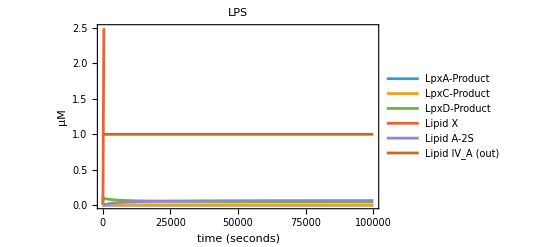

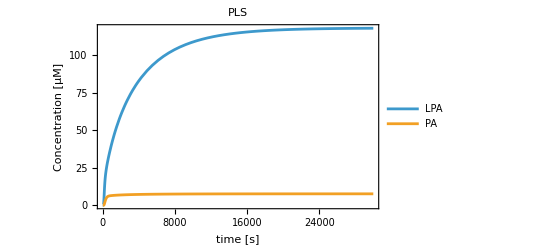

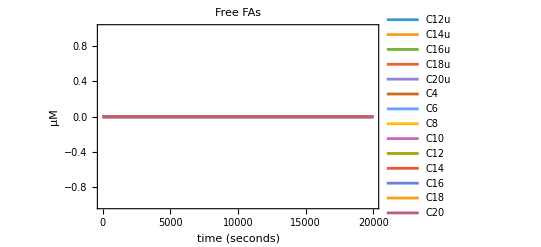

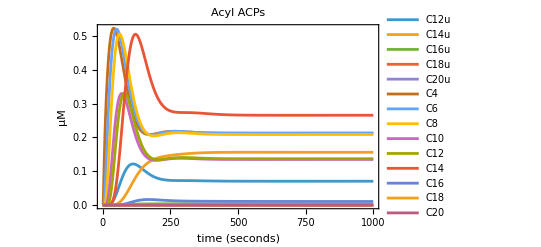

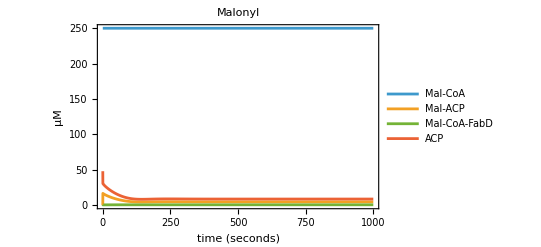

```mathematica
ODEsFinal=ODEs/.kinParamsFAS/.kinParamsLiPh/.kinParamsIO/.enzymeConcsFAS/.enzymeConcsLPS/.enzymeConcsPLS/.(y2ref->0)
ODEsFinal=ODEsFinal/.(y8ref->malCoaConc);
ODEsFinal//TableForm
initsFinal=inits/.kinParamsIO;
initsFinal=initsFinal/.(y4[0]==_:>y4[0]==ACPconc);
Cases[ODEsFinal,_Symbol?(StringContainsQ[ToString[#],"ref"]&),Infinity]
Cases[ODEsFinal/. Thread[Join[{t},vars]->1.],_Symbol,Infinity]//Union
tsol=NDSolve[Join[ODEsFinal,initsFinal],vars,{t,0,100000}];

(* Plot Mal-CoA, PLS and LPS as a check *)
labelsLPS={"LpxA-Product","LpxC-Product","LpxD-Product","Lipid X","Lipid A-2S","Lipid IV_A (out)"};
plotLPS=Plot[Evaluate[{
yL2[t],yL3[t],yL4[t],yL5[t],yL7[t],1}/.tsol],{t,0,100000},
Frame->True,FrameLabel->{"time (seconds)", "μM"}, PlotLabel->"LPS",PlotLegends->labelsLPS];
labelsPLS={"LPA","PA"};
plotPLS=Plot[Evaluate[{
yP2[t],yP3[t]}/.tsol],{t,0,30000},
Frame->True,FrameLabel->{"time [s]", "Concentration [μM]"}, PlotLabel->"PLS",PlotLegends->Placed[labelsPLS,After]];
labelsCs={"C12u","C14u","C16u","C18u","C20u","C4","C6","C8","C10","C12","C14","C16","C18","C20"};
freeFAs={y42[t],y52[t],y62[t],y72[t],y82[t],y16[t],y21[t],y26[t],y31[t],y37[t],y47[t],y57[t],y67[t],y77[t]};
plotFreeFAs=Plot[Evaluate[freeFAs/.tsol],{t,0,20000},
Frame->True,FrameLabel->{"time (seconds)", "μM"}, PlotLabel->"Free FAs",PlotLegends->labelsCs];
acylACPs={y41[t],y51[t],y61[t],y71[t],y81[t],y15[t],y20[t],y25[t],y30[t],y36[t],y46[t],y56[t],y66[t],y76[t]};
plotAcylACPs=Plot[Evaluate[acylACPs/.tsol],{t,0,1000},
Frame->True,FrameLabel->{"time (seconds)", "μM"}, PlotLabel->"Acyl ACPs",PlotLegends->labelsCs];
plotMalACP=Plot[Evaluate[{malCoaConc,y10[t],y87[t],y4[t]}/.tsol],{t,0,1000},
Frame->True,FrameLabel->{"time (seconds)", "μM"},PlotLabel->"Malonyl",PlotLegends->{"Mal-CoA","Mal-ACP","Mal-CoA-FabD","ACP"}];
Show[plotLPS]
Show[plotPLS]
Show[plotFreeFAs]
Show[plotAcylACPs]
Show[plotMalACP]
```

Get steady state concentrations

```mathematica
(*This replaces yXXX'[t]==functions with just the functions*)
steadyStateEqs=ODEsFinal/. {Equal[Derivative[1][_][t],rhs_]:>rhs,(var_)[t]:>var};
varsSS=vars/.(var_)[t]:>var;
timeSS=99000;
rhsReplaceMap=Thread[vars->varsSS];
steadyStateEqs=steadyStateEqs/.rhsReplaceMap;
initialGuessValues=(vars/. tsol/. t->timeSS)[[1]];
guessPairs=Thread[{varsSS,initialGuessValues}];
tsolSS=FindRoot[Thread[steadyStateEqs==0],guessPairs,MaxIterations->10000];
JPL=(v61PlsC+v71PlsC+v56PlsC+v81PlsC)/.ratesPLS/.tsolSS/.kinParamsLiPh/.enzymeConcsPLS/.(var_)[t]:>var
JLP=(vLpxK)/.ratesLPS/.tsolSS/.kinParamsLiPh/.enzymeConcsLPS/.(var_)[t]:>var
JFAS=(k24f y89-k24r e2[t] y10)/. enzymeEqsFAS/. tsolSS/. kinParamsFAS/. enzymeConcsFAS/. (var_)[t]:>var (* Release of FabD and Mal-ACP *)
JACPs=Total[RatesAcACPs]/. tsolSS/. kinParamsFAS/. enzymeConcsFAS
Print[y89/.tsolSS,e2tot/.enzymeEqsFAS/.enzymeConcsFAS/.tsolSS]
ODEsFinal[[79]]//TableForm
ODEs[[79]]//TableForm
(* Check the steady state equations (largest value) *)
steadyStateEqs/. tsolSS//Abs//Max (* <1e-10 OK *)
steadyStateEqs/. tsolSS//Abs//Mean (* <1e-10 OK *)
```

0.0830865

0.00368064

1.25263

1.17637

0.1839251.73914

y88'[t]==60222.9 y87[t]-40213.9 y88[t]-77.292 y4[t] y88[t]+3091.68 y89[t]

y88'[t]==k22f y87[t]-k22r y9ref y88[t]-k23f y4[t] y88[t]+k23r y89[t]

3.45608×10^-11

1.50441×10^-13

## Simulate Steady State Concentrations

As a function of a fixed Mal-CoA concentration

```mathematica
(*Target concentrations and intermediates to track*)ConcMalCoA={25,50,75,100,150,200,300,400,500,750};
concsToPlot={yP3[t],yP2[t],y23[t],y24[t],y25[t],y45[t],yL7[t]};
allRateRules=Join[ratesFAS,ratesLPS,ratesPLS];
allRateRules=DeleteDuplicatesBy[allRateRules,First]

FattyAcidsAsFunction[malCoA_,concs_]:=Module[{ODEsFinalLocal,initsFinalLocal,tsol,tsolSS,steadyStateEqs,varsSS,rhsReplaceMap,initialGuessValues,guessPairs,timeSS,evaluatedConcs,rateSymbols,evaluatedRates,fixedConcsRules},
timeSS=99000;
(*Setup initial conditions*)
initsFinalLocal=inits/. kinParamsIO;
initsFinalLocal=initsFinalLocal/. (y4[0]==_:>y4[0]==ACPconc);
fixedConcsRules=Cases[kinParamsIO,(key_->val_)/;StringEndsQ[SymbolName[key],"ref"]:>(ToExpression[StringDrop[SymbolName[key],-3]]->val)];
(*Setup ODEs: Substitute the parameter for Malonyl-CoA concentration here*)ODEsFinalLocal=ODEs/. kinParamsFAS/. kinParamsLiPh/. kinParamsIO/. enzymeConcsFAS/. enzymeConcsLPS/. enzymeConcsPLS/. (y2ref->0);
ODEsFinalLocal=ODEsFinalLocal/. (y8ref->malCoA);
(*Run NDSolve to get close to steady state-provides initial guess*)
tsol=NDSolve[Join[ODEsFinalLocal,initsFinalLocal],vars,{t,0,timeSS}];
(*Convert ODEs to algebraic equations*)
steadyStateEqs=ODEsFinalLocal/. {Equal[Derivative[1][_][t],rhs_]:>rhs,(var_)[t]:>var};
varsSS=vars/. (var_)[t]:>var;
rhsReplaceMap=Thread[vars->varsSS];
steadyStateEqs=steadyStateEqs/. rhsReplaceMap;
(*Get initial guess from NDSolve solution*)
initialGuessValues=(vars/. tsol/. t->timeSS)[[1]];
guessPairs=Thread[{varsSS,initialGuessValues}];
(*Solve for exact steady state*)
tsolSS=FindRoot[Thread[steadyStateEqs==0],guessPairs,MaxIterations->50000];
(*Calculate fluxes using steady state solution*)
rateSymbols=Keys[allRateRules];
evaluatedRates=rateSymbols/. allRateRules/. kinParamsFAS/. kinParamsLiPh/. kinParamsIO/. enzymeConcsFAS/. enzymeConcsLPS/. enzymeConcsPLS/.(var_)[t]:>var/.tsolSS/.fixedConcsRules/.(y8->malCoA);
(*Evaluate requested intermediate concentrations*)
evaluatedConcs=concs/. (var_)[t]:>var/. tsolSS/. kinParamsIO;
(*Output text to track progress*);
Print["Max SS Fit Error: ",steadyStateEqs/. tsolSS//Abs//Max, " | Mean SS Fit Error: ", steadyStateEqs/. tsolSS//Abs//Mean (* <1e-10 OK *)];
(*Return a flattened list representing one row of data*)
Flatten[{malCoA,evaluatedRates,evaluatedConcs}]]

(*Map the function across all target concentrations using Table*)
simData=Table[FattyAcidsAsFunction[conc,vars],{conc,ConcMalCoA}];

(*Create a formatted table with headers for easy reading*)
headers=Flatten[{"MalCoA",ToString/@Keys[allRateRules],vars/. (var_)[t]:>ToString[var]}];
exportData=Prepend[simData,headers];
exportData//TableForm
If[doExport==True,
Export[FileNameJoin[NotebookDirectory[],"raw_output","simdata_final_model.csv"],exportData],
Nothing[]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 50000 iterations.

Max SS Fit Error: 0.000742714 | Mean SS Fit Error: 8.91957×10^-6

Max SS Fit Error: 2.45564×10^-11 | Mean SS Fit Error: 1.12501×10^-13

Max SS Fit Error: 1.18234×10^-11 | Mean SS Fit Error: 5.03802×10^-14

Max SS Fit Error: 3.63798×10^-12 | Mean SS Fit Error: 3.61369×10^-14

Max SS Fit Error: 6.36646×10^-12 | Mean SS Fit Error: 8.58975×10^-14

Max SS Fit Error: 1.36424×10^-11 | Mean SS Fit Error: 1.51954×10^-13

Max SS Fit Error: 6.36646×10^-12 | Mean SS Fit Error: 6.15905×10^-14

Max SS Fit Error: 1.45519×10^-11 | Mean SS Fit Error: 1.91535×10^-13

Max SS Fit Error: 1.36424×10^-11 | Mean SS Fit Error: 9.64681×10^-14

Max SS Fit Error: 2.45564×10^-11 | Mean SS Fit Error: 1.76275×10^-13

MalCoA | v11 | v12 | v13 | v31 | v23 | vcat71 | vcat72 | vcat73 | vcat74 | vcat75 | vcat76 | vcat77 | vcat78 | vcat79 | vcat75d | vcat76d | vcat77d | vcat78d | vcat79d | v821 | v822 | v823 | v824 | v825 | v826 | v827 | v828 | v825d | v826d | v827d | v828d | v1021 | v1022 | v1023 | v1024 | v1025 | v1026 | v1027 | v1028 | v1025d | v1026d | v1027d | v1028d | v1024d | v3inh | v4inh | v5inh | v6inh | v7inh | v8inh | v9inh | v10inh | v411 | v611 | vcat12 | v21 | v22 | v32 | v24 | v33 | v831 | v832 | v833 | v834 | v835 | v836 | v837 | v838 | v835d | v836d | v837d | v838d | v1031 | v1032 | v1033 | v1034 | v1035 | v1036 | v1037 | v1038 | v1035d | v1036d | v1037d | v1038d | v1034d | vcat3 | vcat81 | vcat82 | vcat83 | vcat84 | vcat85 | vcat86 | vcat87 | vcat88 | vcat8un5 | vcat8un6 | vcat8un7 | vcat8un8 | vcat101 | vcat102 | vcat103 | vcat104 | vcat105 | vcat106 | vcat107 | vcat108 | vcat10un4 | vcat10un5 | vcat10un6 | vcat10un7 | vcat10un8 | v421 | v422 | v423 | v424 | v425 | v426 | v427 | v428 | v429 | v425d | v426d | v427d | v428d | v429d | vcat41 | v511 | v911 | vcat42 | v512 | v912 | vcat43 | v513 | v913 | vcat44 | v514 | v914 | vcat45 | v515 | v915 | vcat46 | v516 | v916 | vcat47 | v517 | v917 | vcat48 | v518 | v918 | vcat49 | v519 | v919 | vcat45d | v515d | v91un5 | vcat46d | v516d | v91un6 | vcat47d | v517d | v91un7 | vcat48d | v518d | v91un8 | vcat49d | v519d | v91un9 | v531 | v931 | v621 | v532 | v932 | v622 | v533 | v933 | v623 | v534 | v934 | v624 | v535 | v935 | v625 | v536 | v936 | v626 | v537 | v937 | v627 | v538 | v938 | v628 | v539 | v939 | v629 | v93un4 | v1014 | v535d | v935d | v625d | v536d | v936d | v626d | v537d | v937d | v627d | v538d | v938d | v628d | v539d | v939d | v629d | vcat61 | v711 | v811 | v1011 | v341 | v351 | vcat62 | v712 | v812 | v1012 | v342 | v352 | vcat63 | v713 | v813 | v1013 | v343 | v353 | vcat64 | v714 | v814 | v1014d | v344 | v354 | vcat65 | v715 | v815 | v1015 | v345 | v355 | vcat66 | v716 | v816 | v1016 | v346 | v356 | vcat67 | v717 | v817 | v1017 | v347 | v357 | vcat68 | v718 | v818 | v1018 | v348 | v358 | vcat69 | v719 | v349 | v359 | vcat65d | v715d | v815d | v1015d | v345d | v355d | vcat66d | v716d | v816d | v1016d | v346d | v356d | vcat67d | v717d | v817d | v1017d | v347d | v357d | vcat68d | v718d | v818d | v1018d | v348d | v358d | vcat69d | v719d | v349d | v359d | vcat11 | vcat51 | vcat52 | vcat53 | vcat54 | vcat55 | vcat56 | vcat57 | vcat58 | vcat59 | vcat55d | vcat56d | vcat57d | vcat58d | vcat59d | vcat91 | vcat92 | vcat93 | vcat94 | vcat95 | vcat96 | vcat97 | vcat98 | vcat99 | vcat95d | vcat96d | vcat97d | vcat98d | vcat99d | vcat9un4 | vLpxA | vLpxC | vLpxD | vLpxH | vLpxB | vLpxK | vLpxL | vLpxM | v56PlsB | v61PlsB | v66PlsB | v71PlsB | v76PlsB | v56PlsC | v61PlsC | v71PlsC | v81PlsC | vCdsA | y4 | y10 | y12 | y17 | y22 | y27 | y33 | y43 | y53 | y63 | y73 | y38 | y48 | y58 | y68 | y78 | y13 | y18 | y23 | y28 | y34 | y44 | y54 | y64 | y74 | y39 | y49 | y59 | y69 | y79 | y14 | y19 | y24 | y29 | y35 | y45 | y55 | y65 | y75 | y32 | y40 | y50 | y60 | y70 | y80 | y15 | y20 | y25 | y30 | y36 | y46 | y56 | y66 | y76 | y41 | y51 | y61 | y71 | y81 | y16 | y21 | y26 | y31 | y37 | y47 | y57 | y67 | y77 | y42 | y52 | y62 | y72 | y82 | y83 | y84 | y85 | y86 | y87 | y88 | y89 | y90 | y91 | y92 | y93 | y97 | y112 | y127 | y142 | y157 | y172 | y187 | y202 | y217 | y226 | y241 | y256 | y271 | y286 | y98 | y113 | y128 | y143 | y158 | y173 | y188 | y203 | y218 | y227 | y242 | y257 | y272 | y287 | y99 | y114 | y129 | y144 | y159 | y174 | y189 | y204 | y219 | y228 | y243 | y258 | y273 | y288 | y105 | y120 | y135 | y150 | y165 | y180 | y195 | y210 | y222 | y234 | y249 | y264 | y279 | y291 | y106 | y121 | y136 | y151 | y166 | y181 | y196 | y211 | y223 | y301 | y235 | y250 | y265 | y280 | y292 | y94 | y100 | y115 | y130 | y145 | y160 | y175 | y190 | y205 | y220 | y229 | y244 | y259 | y274 | y289 | y101 | y116 | y131 | y146 | y161 | y176 | y191 | y206 | y221 | y230 | y245 | y260 | y275 | y290 | y102 | y117 | y132 | y147 | y162 | y177 | y192 | y207 | y231 | y246 | y261 | y276 | y103 | y118 | y133 | y148 | y163 | y178 | y193 | y208 | y232 | y247 | y262 | y277 | y104 | y119 | y134 | y149 | y164 | y179 | y194 | y209 | y233 | y248 | y263 | y278 | y107 | y122 | y137 | y152 | y167 | y182 | y197 | y212 | y236 | y251 | y266 | y281 | y108 | y123 | y138 | y153 | y168 | y183 | y198 | y213 | y237 | y252 | y267 | y282 | y109 | y124 | y139 | y154 | y169 | y184 | y199 | y214 | y238 | y253 | y268 | y283 | y302 | y303 | y304 | y95 | y110 | y125 | y140 | y155 | y170 | y185 | y200 | y215 | y224 | y239 | y254 | y269 | y284 | y96 | y111 | y126 | y141 | y156 | y171 | y186 | y201 | y216 | y225 | y240 | y255 | y270 | y285 | y297 | y293 | y294 | y295 | y296 | y298 | y299 | y300 | yL2 | yL3 | yL4 | yL5 | yL7 | yP2 | yP3
25 | -3.80115×10^-14 | 4.66565×10^-15+3.97805×10^-16 y2 | -2.78946×10^-15 | 0.0311776 | 0.210361 | -7.69458×10^-15 | -7.49191×10^-15 | -1.06202×10^-14 | -1.67402×10^-15 | -3.94961×10^-15 | 2.67963×10^-14 | -2.10957×10^-14 | -2.28809×10^-14 | -2.29914×10^-14 | -7.94487×10^-15 | -6.98651×10^-15 | -1.42577×10^-14 | -1.94055×10^-14 | -1.52388×10^-14 | 0.0197769 | 0.0197769 | 0.0192756 | 0.0182728 | 0.0178941 | 0.0170541 | 8.51409×10^-6 | 1.44882×10^-8 | 0.00129227 | 0.00165271 | 9.13729×10^-7 | 6.56277×10^-10 | 0.0114062 | 0.0114062 | 0.0119073 | 0.0108097 | 0.0111884 | 0.00463087 | 3.94137×10^-6 | 6.76872×10^-9 | 0.000808051 | 0.00044998 | 4.78506×10^-8 | 3.56572×10^-11 | 0.00210043 | -6.6265×10^-11 | -5.05756×10^-10 | -1.68269×10^-8 | -4.87533×10^-9 | 2.97692×10^-14 | -8.11227×10^-9 | -7.13942×10^-8 | -5.86756×10^-8 | 0.210872 | 0.201388 | -9.02215×10^-15 | 0.210872 | 0.210872 | 0.0311776 | 0.211104 | 0.0311759 | 0.0197752 | 0.0197752 | 0.019274 | 0.018272 | 0.0178934 | 0.0170621 | 8.33573×10^-6 | 1.39107×10^-8 | 0.0012914 | 0.00165057 | 9.10694×10^-7 | 6.52453×10^-10 | 0.0114024 | 0.0114024 | 0.0119036 | 0.0108069 | 0.0111855 | 0.0046322 | 3.80119×10^-6 | 6.34337×10^-9 | 0.000807285 | 0.000448112 | 4.55589×10^-8 | 3.27128×10^-11 | 0.00209869 | 0.0311776 | 0.0197752 | 0.0197752 | 0.019274 | 0.018272 | 0.0178934 | 0.0170621 | 8.33622×10^-6 | 1.39121×10^-8 | 0.00129141 | 0.00165058 | 9.10702×10^-7 | 6.52383×10^-10 | 0.0114024 | 0.0114024 | 0.0119036 | 0.0108069 | 0.0111855 | 0.0046322 | 3.80157×10^-6 | 6.34436×10^-9 | 0.00209869 | 0.000807287 | 0.000448117 | 4.5565×10^-8 | 3.264×10^-11 | 0.0311775 | 0.0311775 | 0.0311775 | 0.0311775 | 0.0290789 | 0.0290789 | 0.0216942 | 0.0000121378 | 2.02566×10^-8 | 0.00209869 | 0.00209869 | 0.00209869 | 9.56267×10^-7 | 6.85028×10^-10 | 0.0311776 | 0.023498 | 0.00767879 | 0.0311776 | 0.0200981 | 0.0110786 | 0.0311776 | 0.0045403 | 0.026636 | 0.0311776 | 0.00353867 | 0.0276376 | 0.0290789 | 0.00224134 | 0.0268363 | 0.0290789 | 0.00548495 | 0.0162085 | 0.0216943 | 0.0130043 | 0.00868929 | 0.0000121378 | 7.27579×10^-6 | 4.86162×10^-6 | 2.02565×10^-8 | 1.21422×10^-8 | 8.11337×10^-9 | 0.00209869 | 0.00186712 | 0.000231529 | 0.00209869 | 0.00192726 | 0.000171397 | 0.00209869 | 0.00206271 | 0.0000359529 | 9.56268×10^-7 | 9.39891×10^-7 | 1.63825×10^-8 | 6.85029×10^-10 | 6.73304×10^-10 | 1.17351×10^-11 | 0.0234985 | 0.00767913 | 0.0311776 | 0.0200985 | 0.0110791 | 0.0311776 | 0.00454043 | 0.0266372 | 0.0311776 | 0.00353879 | 0.0255402 | 0.0290789 | 0.00224142 | 0.0268375 | 0.0290789 | 0.00548506 | 0.0162092 | 0.0216942 | 0.0130046 | 0.00868969 | 0.0216942 | 7.27588×10^-6 | 4.86176×10^-6 | 0.0000121376 | 1.21421×10^-8 | 8.11334×10^-9 | 2.02553×10^-8 | 0.00209918 | 0.0020981 | 0.00186715 | 0.000231548 | 0.00209869 | 0.00192729 | 0.000171404 | 0.00209869 | 0.00206274 | 0.0000359547 | 0.00209869 | 9.399×10^-7 | 1.6383×10^-8 | 9.56282×10^-7 | 6.73308×10^-10 | 1.17381×10^-11 | 6.85051×10^-10 | 0.0311776 | 2.217×10^-14 | 0.01977 | 0.0113985 | -1.1214×10^-9 | -3.0036×10^-9 | 0.0311776 | 2.43843×10^-14 | 0.01977 | 0.0113985 | -1.1214×10^-9 | -3.0036×10^-9 | 0.0311776 | 2.13176×10^-14 | 0.0192689 | 0.0118997 | -1.09992×10^-9 | -2.94606×10^-9 | 0.0290789 | 3.30705×10^-14 | 0.0182673 | 0.0108033 | -1.01321×10^-9 | -2.71385×10^-9 | 0.0290789 | 3.42533×10^-14 | 0.0178886 | 0.0111819 | -1.03322×10^-9 | -2.76741×10^-9 | 0.0216943 | 8.86126×10^-14 | 0.0170532 | 0.00462539 | -1.94105×10^-9 | -5.199×10^-9 | 0.0216943 | 4.12767×10^-15 | 8.31129×10^-6 | 3.7823×10^-6 | -5.25704×10^-12 | -1.12373×10^-11 | 0.0000121376 | 2.99074×10^-15 | 1.38894×10^-8 | 6.32657×10^-9 | 6.6973×10^-14 | 8.48463×10^-14 | 2.02553×10^-8 | 2.38597×10^-15 | 8.72253×10^-14 | 8.69754×10^-14 | 0.00209869 | 7.30883×10^-15 | 0.00129112 | 0.000807065 | -6.22316×10^-11 | -1.66682×10^-10 | 0.00209869 | 1.19063×10^-14 | 0.00164991 | 0.000447605 | -1.44031×10^-10 | -3.85745×10^-10 | 0.00209869 | 2.28208×10^-15 | 9.10504×10^-7 | 4.54109×10^-8 | -5.07634×10^-14 | -1.40229×10^-13 | 9.56283×10^-7 | 2.53458×10^-15 | 6.52336×10^-10 | 3.25589×10^-11 | -7.68649×10^-15 | 3.56685×10^-15 | 6.85048×10^-10 | 1.58135×10^-15 | 1.9796×10^-16 | -1.69264×10^-15 | -5.47744×10^-17 | 0.0234985 | 0.0200985 | 0.00454042 | 0.00353878 | 0.00224141 | 0.00548506 | 0.0130046 | 7.27588×10^-6 | 1.21422×10^-8 | 0.00186715 | 0.00192729 | 0.00206274 | 9.399×10^-7 | 6.7331×10^-10 | 0.00767912 | 0.0110791 | 0.0266372 | 0.0276388 | 0.0268375 | 0.0162092 | 0.00868969 | 4.86176×10^-6 | 8.11342×10^-9 | 0.000231546 | 0.000171404 | 0.0000359546 | 1.6383×10^-8 | 1.1735×10^-11 | 0.00209869 | 0.0036923 | 0.00369232 | 0.0036923 | 0.00185567 | 0.00183665 | 0.00183665 | 0 | 0 | 0.0121013 | 6.60316×10^-6 | 0.0000121174 | 5.67648×10^-8 | 2.02549×10^-8 | 0.00958081 | 0.00209113 | 8.98833×10^-7 | 6.85063×10^-10 | 0.0116724 | 14.5795 | 0.797013 | 0.0269159 | 0.0269159 | 0.0269159 | 0.0269159 | 0.0251041 | 0.0251041 | 0.0187289 | 0.0000104787 | 1.74877×10^-8 | 0.00181182 | 0.00181182 | 0.00181182 | 8.25556×10^-7 | 5.91392×10^-10 | 0.444417 | 0.184742 | 0.197406 | 0.148471 | 0.189129 | 0.901409 | 1.09341 | 0.000611751 | 1.0209×10^-6 | 0.088487 | 0.30967 | 0.173037 | 0.0000788455 | 5.6482×10^-8 | 0.00646751 | 0.00646751 | 0.00646751 | 0.00603215 | 0.00603215 | 0.00450028 | 0.00450028 | 2.51784×10^-6 | 4.20178×10^-9 | 0.0612896 | 0.000435355 | 0.000435355 | 0.000435355 | 1.98372×10^-7 | 1.42107×10^-10 | 0.358852 | 0.358852 | 0.351711 | 0.320533 | 0.326659 | 0.568884 | 0.00250424 | 4.17928×10^-6 | 1.39718×10^-7 | 0.0235758 | 0.0550336 | 0.0000273291 | 1.95781×10^-8 | 2.98437×10^-10 | 7.66593×10^-9 | 4.21697×10^-10 | -1.0478×10^-9 | 2.41128×10^-9 | -1.03899×10^-9 | 5.21508×10^-10 | 3.47948×10^-9 | 1.21848×10^-9 | 5.57427×10^-9 | 3.73661×10^-9 | 1.90477×10^-9 | 8.86282×10^-10 | 7.71298×10^-10 | 1.05047×10^-8 | 1.30897×10^-14 | -6.14089×10^-17 | -5.18408×10^-16 | -1.25295×10^-14 | 0.3195 | 0.478466 | 0.174327 | 0.385157 | 0.0135144 | 0.00214414 | 0.494929 | 0.000594512 | 0.000594512 | 0.000594512 | 0.000594512 | 0.000554493 | 0.000554493 | 0.000413679 | 2.3145×10^-7 | 3.86263×10^-10 | 0.0000400191 | 0.0000400191 | 0.0000400191 | 1.82347×10^-8 | 1.30625×10^-11 | 0.000618805 | 0.000552895 | 0.000185895 | 0.000180278 | 0.00012457 | 0.000148151 | 0.00034048 | 1.90494×10^-7 | 3.17899×10^-10 | 0.0000533178 | 0.000050635 | 0.0000538536 | 2.45388×10^-8 | 1.75786×10^-11 | 0.000144529 | 0.000129512 | 0.0000444776 | 0.0000434976 | 0.0000301422 | 0.0000346614 | 0.0000794911 | 4.44742×10^-8 | 7.42192×10^-11 | 0.0000125192 | 0.0000118245 | 0.0000125706 | 5.72789×10^-9 | 4.10325×10^-12 | 0.000538388 | 0.000857235 | 0.002038 | 0.00213963 | 0.00204448 | 0.00108817 | 0.000581089 | 3.25112×10^-7 | 5.42552×10^-10 | 0.0000355661 | 0.0000135521 | 3.37234×10^-6 | 1.53663×10^-9 | 1.10079×10^-12 | 0.0000550898 | 0.0000995622 | 0.000233628 | 0.000248652 | 0.000233179 | 0.000104239 | 0.000055315 | 3.0948×10^-8 | 5.16462×10^-11 | 0.000965179 | 6.48529×10^-6 | 1.61267×10^-6 | 4.70431×10^-7 | 2.14355×10^-10 | 1.53569×10^-13 | 0.855956 | 0.0000876906 | 0.0000876906 | 0.0000876906 | 0.0000817877 | 0.0000817877 | 0.0000610176 | 0.0000610176 | 3.41385×10^-8 | 5.69703×10^-11 | 5.90281×10^-6 | 5.90281×10^-6 | 5.90281×10^-6 | 2.68966×10^-9 | 1.92678×10^-12 | -2.32789×10^-13 | -2.52931×10^-13 | -1.76326×10^-13 | -1.82066×10^-13 | -2.6873×10^-14 | 1.00498×10^-13 | -3.62511×10^-14 | -3.2202×10^-14 | -2.57083×10^-14 | -5.40566×10^-14 | -2.62024×10^-14 | -2.45005×10^-14 | -2.73109×10^-14 | -1.70397×10^-14 | 0.00846566 | 0.00846566 | 0.00829785 | 0.007558 | 0.00770686 | 0.0135072 | 0.0000598639 | 9.99055×10^-8 | 0.000556222 | 0.00130668 | 6.4833×10^-7 | 4.64453×10^-10 | 0.00203414 | 0.00203414 | 0.00199384 | 0.00181594 | 0.00185184 | 0.00324801 | 0.0000144066 | 2.40428×10^-8 | 0.000133651 | 0.00031421 | 1.55884×10^-7 | 1.11673×10^-10 | 0.0000777678 | 0.0000777678 | 0.0000768905 | 0.0000656768 | 0.000071462 | 0.000212207 | 1.34971×10^-6 | 2.25251×10^-9 | 5.15758×10^-6 | 0.0000205288 | 9.62772×10^-9 | 6.89683×10^-12 | 0.00596155 | 0.00596155 | 0.0058385 | 0.0053212 | 0.00542185 | 0.00953233 | 0.0000420621 | 7.01965×10^-8 | 0.000391308 | 0.000922153 | 4.59004×10^-7 | 3.28823×10^-10 | 0.00143288 | 0.00143288 | 0.00140318 | 0.00127886 | 0.00130302 | 0.00229345 | 0.0000101229 | 1.68938×10^-8 | 0.0000940422 | 0.000221867 | 1.10465×10^-7 | 7.91352×10^-11 | 0.0000701112 | 0.0000701112 | 0.0000641846 | 0.0000587532 | 0.0000588049 | 0.00019482 | 9.60852×10^-7 | 1.60354×10^-9 | 4.24409×10^-6 | 0.0000188468 | 1.04605×10^-8 | 7.49326×10^-12 | 0.00101728 | 0.00024448 | 0.0000110333 | 6.07487×10^-6 | 6.07487×10^-6 | 5.95399×10^-6 | 5.42619×10^-6 | 5.52989×10^-6 | 0.0000506226 | 1.89951×10^-7 | 1.21939×10^-9 | 7.96132×10^-11 | 3.99106×10^-7 | 4.89721×10^-6 | 2.07296×10^-9 | 5.71264×10^-12 | 1.70053×10^-13 | 0.000591425 | 0.000591425 | 0.000579656 | 0.000528272 | 0.000538368 | 0.000737294 | 0.0000129393 | 1.92169×10^-8 | 2.17231×10^-9 | 0.0000388553 | 0.0000713255 | 1.41209×10^-7 | 9.00223×10^-11 | 4.64144×10^-12 | 4.61759×10^-14 | 0.00283345 | 0.0157062 | 0.0784881 | 0.078983 | 0.037331 | 0.333925 | 0.245043 | 0.000135042 | 0.00415614 | 0.0248129 | 79.7306 | 0.0326912 | 684.797 | 1.0327
50 | -7.13807×10^-19 | 3.20325×10^-20+1.9967×10^-21 y2 | -1.7893×10^-20 | 0.0841453 | 0.575982 | -6.57621×10^-17 | -5.96015×10^-17 | -8.25336×10^-17 | -7.59244×10^-18 | -5.42321×10^-18 | 3.4382×10^-16 | -1.75124×10^-16 | -1.84612×10^-16 | -1.86824×10^-16 | -1.28019×10^-16 | -8.54561×10^-17 | -1.82171×10^-16 | -1.84655×10^-16 | -1.86804×10^-16 | 0.0536548 | 0.0536548 | 0.0523251 | 0.0469736 | 0.0460236 | 0.0482914 | 0.0000414909 | 1.1697×10^-7 | 0.00606484 | 0.00772528 | 7.79956×10^-6 | 1.01932×10^-8 | 0.0304906 | 0.0304906 | 0.0318202 | 0.0273744 | 0.0283244 | 0.0129526 | 0.0000186027 | 5.24442×10^-8 | 0.00373249 | 0.00207205 | 3.86893×10^-7 | 5.05626×10^-10 | 0.00979733 | 3.92264×10^-16 | 3.86843×10^-16 | 3.83374×10^-16 | 4.00721×10^-16 | 2.29917×10^-16 | 3.88578×10^-16 | 3.81639×10^-16 | 3.71231×10^-16 | 0.575982 | 0.55308 | -4.51975×10^-20 | 0.575982 | 0.575982 | 0.0841453 | 0.575982 | 0.0841453 | 0.0536548 | 0.0536548 | 0.0523251 | 0.0469736 | 0.0460236 | 0.0482914 | 0.0000414909 | 1.1697×10^-7 | 0.00606484 | 0.00772528 | 7.79956×10^-6 | 1.01932×10^-8 | 0.0304906 | 0.0304906 | 0.0318202 | 0.0273744 | 0.0283244 | 0.0129526 | 0.0000186027 | 5.24442×10^-8 | 0.00373249 | 0.00207205 | 3.86893×10^-7 | 5.05626×10^-10 | 0.00979733 | 0.0841453 | 0.0536548 | 0.0536548 | 0.0523251 | 0.0469736 | 0.0460236 | 0.0482914 | 0.0000414909 | 1.1697×10^-7 | 0.00606484 | 0.00772528 | 7.79956×10^-6 | 1.01931×10^-8 | 0.0304906 | 0.0304906 | 0.0318202 | 0.0273744 | 0.0283244 | 0.0129526 | 0.0000186027 | 5.24442×10^-8 | 0.00979733 | 0.00373249 | 0.00207205 | 3.86893×10^-7 | 5.05626×10^-10 | 0.0841453 | 0.0841453 | 0.0841453 | 0.0841453 | 0.074348 | 0.074348 | 0.061244 | 0.0000600935 | 1.69414×10^-7 | 0.00979733 | 0.00979733 | 0.00979733 | 8.18645×10^-6 | 1.06988×10^-8 | 0.0841453 | 0.0633052 | 0.0208401 | 0.0841453 | 0.0540098 | 0.0301356 | 0.0841453 | 0.0124531 | 0.0716923 | 0.0841453 | 0.00981103 | 0.0743343 | 0.074348 | 0.00599887 | 0.0683492 | 0.074348 | 0.01546 | 0.0457839 | 0.061244 | 0.0366541 | 0.0245898 | 0.0000600935 | 0.0000359656 | 0.0000241279 | 1.69414×10^-7 | 1.01393×10^-7 | 6.80209×10^-8 | 0.00979733 | 0.00863475 | 0.00116258 | 0.00979733 | 0.00898389 | 0.000813442 | 0.00979733 | 0.00962349 | 0.000173839 | 8.18645×10^-6 | 8.04119×10^-6 | 1.45257×10^-7 | 1.06988×10^-8 | 1.05089×10^-8 | 1.89835×10^-10 | 0.0633052 | 0.0208401 | 0.0841453 | 0.0540098 | 0.0301356 | 0.0841453 | 0.0124531 | 0.0716923 | 0.0841453 | 0.00981103 | 0.064537 | 0.074348 | 0.00599887 | 0.0683492 | 0.074348 | 0.01546 | 0.0457839 | 0.061244 | 0.0366541 | 0.0245898 | 0.061244 | 0.0000359656 | 0.0000241279 | 0.0000600935 | 1.01393×10^-7 | 6.80209×10^-8 | 1.69414×10^-7 | 0.00979733 | 0.00979733 | 0.00863475 | 0.00116258 | 0.00979733 | 0.00898389 | 0.000813442 | 0.00979733 | 0.00962349 | 0.000173839 | 0.00979733 | 8.04119×10^-6 | 1.45257×10^-7 | 8.18645×10^-6 | 1.05089×10^-8 | 1.89834×10^-10 | 1.06988×10^-8 | 0.0841453 | 1.90599×10^-16 | 0.0536548 | 0.0304906 | 4.13732×10^-16 | 3.92048×10^-16 | 0.0841453 | 1.96331×10^-16 | 0.0536548 | 0.0304906 | 4.12864×10^-16 | 3.90313×10^-16 | 0.0841453 | 1.79345×10^-16 | 0.0523251 | 0.0318202 | 4.12864×10^-16 | 3.93782×10^-16 | 0.074348 | 2.38046×10^-16 | 0.0469736 | 0.0273744 | 4.10262×10^-16 | 3.90313×10^-16 | 0.074348 | 3.2034×10^-16 | 0.0460236 | 0.0283244 | 4.09395×10^-16 | 3.92048×10^-16 | 0.061244 | 9.48333×10^-16 | 0.0482914 | 0.0129526 | 4.28477×10^-16 | 3.95517×10^-16 | 0.061244 | 4.24581×10^-17 | 0.0000414909 | 0.0000186027 | 3.90665×10^-16 | 3.90367×10^-16 | 0.0000600935 | 2.41848×10^-17 | 1.1697×10^-7 | 5.24442×10^-8 | 3.90389×10^-16 | 3.90396×10^-16 | 1.69414×10^-7 | 1.93942×10^-17 | 3.90402×10^-16 | 3.90397×10^-16 | 0.00979733 | 1.22598×10^-16 | 0.00606484 | 0.00373249 | 3.92806×10^-16 | 3.9053×10^-16 | 0.00979733 | 2.00594×10^-16 | 0.00772528 | 0.00207205 | 3.95951×10^-16 | 3.90313×10^-16 | 0.00979733 | 2.9327×10^-17 | 7.79956×10^-6 | 3.86893×10^-7 | 6.21023×10^-16 | 3.90337×10^-16 | 8.18645×10^-6 | 2.41185×10^-17 | 1.01932×10^-8 | 5.05627×10^-10 | 3.90331×10^-16 | 3.9034×10^-16 | 1.06988×10^-8 | 1.93849×10^-17 | 3.90341×10^-16 | 3.90338×10^-16 | -3.76059×10^-22 | 0.0633052 | 0.0540098 | 0.0124531 | 0.00981103 | 0.00599887 | 0.01546 | 0.0366541 | 0.0000359656 | 1.01393×10^-7 | 0.00863475 | 0.00898389 | 0.00962349 | 8.04119×10^-6 | 1.05089×10^-8 | 0.0208401 | 0.0301356 | 0.0716923 | 0.0743343 | 0.0683492 | 0.0457839 | 0.0245898 | 0.0000241279 | 6.80209×10^-8 | 0.00116258 | 0.000813442 | 0.000173839 | 1.45257×10^-7 | 1.89834×10^-10 | 0.00979733 | 0.00655203 | 0.00655203 | 0.00655203 | 0.00327602 | 0.00327602 | 0.00327602 | 0 | 0 | 0.0354265 | 0.0000335444 | 0.0000599241 | 5.26065×10^-7 | 1.69414×10^-7 | 0.0257574 | 0.0097556 | 7.64969×10^-6 | 1.06988×10^-8 | 0.0355206 | 20.0059 | 2.18542 | 0.0743625 | 0.0743625 | 0.0743625 | 0.0743625 | 0.0657043 | 0.0657043 | 0.0541237 | 0.000053107 | 1.49718×10^-7 | 0.00865828 | 0.00865828 | 0.00865828 | 7.23469×10^-6 | 9.45493×10^-9 | 1.34434 | 0.555854 | 0.588956 | 0.430741 | 0.534158 | 2.84788 | 3.46179 | 0.00339676 | 9.57607×10^-6 | 0.457247 | 1.62107 | 0.906982 | 0.000757856 | 9.90433×10^-7 | 0.017924 | 0.017924 | 0.017924 | 0.015837 | 0.015837 | 0.0130457 | 0.0130457 | 0.0000128006 | 3.60873×10^-8 | 0.163286 | 0.00208695 | 0.00208695 | 0.00208695 | 1.74381×10^-6 | 2.27897×10^-9 | 0.547092 | 0.547092 | 0.536469 | 0.463263 | 0.472064 | 0.898407 | 0.0069026 | 0.0000194596 | 1.10031×10^-6 | 0.062207 | 0.14372 | 0.000130718 | 1.70834×10^-7 | 4.77852×10^-9 | -4.68402×10^-10 | -5.77261×10^-10 | -7.78263×10^-10 | -1.59837×10^-9 | 2.00575×10^-9 | 4.10768×10^-10 | -1.22064×10^-9 | 1.56395×10^-9 | 5.97222×10^-10 | 1.83654×10^-9 | 7.63936×10^-10 | 6.40541×10^-10 | 1.08634×10^-9 | -2.89442×10^-9 | 6.5701×10^-20 | -4.21609×10^-22 | -2.59915×10^-21 | -6.27679×10^-20 | 0.391153 | 0.585761 | 0.29278 | 0.37914 | 0.0133019 | 0.00578683 | 0.483488 | 0.00160453 | 0.00160453 | 0.00160453 | 0.00160453 | 0.00141771 | 0.00141771 | 0.00116784 | 1.1459×10^-6 | 3.23049×10^-9 | 0.000186821 | 0.000186821 | 0.000186821 | 1.56104×10^-7 | 2.0401×10^-10 | 0.00166524 | 0.00147903 | 0.000491072 | 0.000461285 | 0.000310835 | 0.000416239 | 0.000959074 | 9.41059×10^-7 | 2.65301×10^-9 | 0.000244853 | 0.000235817 | 0.000251153 | 2.09859×10^-7 | 2.74262×10^-10 | 0.000388906 | 0.000346349 | 0.000117302 | 0.000110981 | 0.0000750417 | 0.0000973626 | 0.000223903 | 2.19698×10^-7 | 6.19366×10^-10 | 0.0000574672 | 0.0000550654 | 0.0000586233 | 4.89845×10^-8 | 6.40172×10^-11 | 0.00145291 | 0.00229974 | 0.00542222 | 0.00552352 | 0.00514944 | 0.00306796 | 0.00164182 | 1.61098×10^-6 | 4.54163×10^-9 | 0.000163458 | 0.0000632422 | 0.0000157424 | 1.3154×10^-8 | 1.71908×10^-11 | 0.00014746 | 0.000262835 | 0.000613093 | 0.000611103 | 0.000579529 | 0.000293024 | 0.000155896 | 1.52968×10^-7 | 4.31244×10^-10 | 0.0023242 | 0.00002879 | 7.38557×10^-6 | 2.13409×10^-6 | 1.7832×10^-9 | 2.33045×10^-12 | 0.83357 | 0.000236668 | 0.000236668 | 0.000236668 | 0.000209112 | 0.000209112 | 0.000172256 | 0.000172256 | 1.6902×10^-7 | 4.76497×10^-10 | 0.0000275561 | 0.0000275561 | 0.0000275561 | 2.30253×10^-8 | 3.00915×10^-11 | -1.98955×10^-15 | -2.01218×10^-15 | -1.3703×10^-15 | -8.25754×10^-16 | -3.68993×10^-17 | 1.28947×10^-15 | -3.00935×10^-16 | -2.59818×10^-16 | -2.08901×10^-16 | -8.71036×10^-16 | -3.20497×10^-16 | -3.13045×10^-16 | -2.59879×10^-16 | -2.08879×10^-16 | 0.0115136 | 0.0115136 | 0.0112918 | 0.00974011 | 0.00993632 | 0.0191486 | 0.000149121 | 4.20397×10^-7 | 0.00130937 | 0.00306325 | 2.78143×10^-6 | 3.63501×10^-9 | 0.0020128 | 0.0020128 | 0.00197406 | 0.00170256 | 0.00173709 | 0.00335263 | 0.0000261503 | 7.37224×10^-8 | 0.000228908 | 0.000536327 | 4.86887×10^-7 | 6.36307×10^-10 | 0.000211003 | 0.000211003 | 0.000208743 | 0.000168842 | 0.000183808 | 0.000600617 | 6.71777×10^-6 | 1.89386×10^-8 | 0.0000242216 | 0.000096082 | 8.2455×10^-8 | 1.07759×10^-10 | 0.00798843 | 0.00798843 | 0.00782166 | 0.00675496 | 0.00688068 | 0.0133433 | 0.00010301 | 2.90402×10^-7 | 0.000906712 | 0.00213456 | 1.95053×10^-6 | 2.54913×10^-9 | 0.00139737 | 0.00139737 | 0.00136795 | 0.0011814 | 0.00120334 | 0.00233878 | 0.0000180654 | 5.09295×10^-8 | 0.000158572 | 0.00037414 | 3.42071×10^-7 | 4.47049×10^-10 | 0.00018748 | 0.00018748 | 0.000171576 | 0.000148824 | 0.000148908 | 0.000544757 | 4.70185×10^-6 | 1.32553×10^-8 | 0.0000196226 | 0.0000871459 | 8.88203×10^-8 | 1.16078×10^-10 | 0.00238001 | 0.000416231 | 0.0000515068 | 9.11696×10^-6 | 9.11696×10^-6 | 8.93994×10^-6 | 7.72×10^-6 | 7.86667×10^-6 | 0.0000786975 | 5.15401×10^-7 | 5.58916×10^-9 | 6.17233×10^-10 | 1.03664×10^-6 | 0.0000125894 | 9.7604×10^-9 | 4.90664×10^-11 | 2.68055×10^-12 | 0.000887491 | 0.000887491 | 0.000870259 | 0.000751504 | 0.000765781 | 0.00114606 | 0.0000351049 | 8.80717×10^-8 | 1.68389×10^-8 | 0.000100912 | 0.000183338 | 6.64798×10^-7 | 7.73169×10^-10 | 7.31296×10^-11 | 1.007×10^-15 | 0.00382735 | 0.0210804 | 0.095833 | 0.10562 | 0.0463327 | 0.408966 | 0.298913 | 0.000239764 | 0.00422129 | 0.0438185 | 80.7075 | 0.0583486 | 597.007 | 3.17306
75 | 3.81191×10^-32 | 0.+3.10943×10^-36 y2 | 2.70932×10^-34 | 0.117718 | 0.80968 | -7.43134×10^-31 | -8.99606×10^-31 | -6.18859×10^-30 | -2.44252×10^-30 | -6.00359×10^-30 | 9.72817×10^-29 | 1.17348×10^-29 | 9.87913×10^-30 | 2.68616×10^-28 | 8.86951×10^-30 | 1.42465×10^-28 | -1.77888×10^-30 | 6.30583×10^-31 | 2.16497×10^-29 | 0.0748927 | 0.0748927 | 0.073054 | 0.0623356 | 0.061089 | 0.0664179 | 0.0000845099 | 3.3439×10^-7 | 0.011638 | 0.0148263 | 0.0000237286 | 4.86745×10^-8 | 0.0428253 | 0.0428253 | 0.044664 | 0.0365448 | 0.0377914 | 0.0179693 | 0.0000380379 | 1.50509×10^-7 | 0.00719959 | 0.00401124 | 1.19144×10^-6 | 2.44401×10^-9 | 0.0188376 | 1.02999×10^-18 | -1.10589×10^-17 | -1.73472×10^-18 | 3.46945×10^-18 | 1.49371×10^-28 | -8.67362×10^-19 | 2.77556×10^-17 | -6.93889×10^-18 | 0.80968 | 0.77635 | -7.15074×10^-35 | 0.80968 | 0.80968 | 0.117718 | 0.80968 | 0.117718 | 0.0748927 | 0.0748927 | 0.073054 | 0.0623356 | 0.061089 | 0.0664179 | 0.0000845099 | 3.3439×10^-7 | 0.011638 | 0.0148263 | 0.0000237286 | 4.86745×10^-8 | 0.0428253 | 0.0428253 | 0.044664 | 0.0365448 | 0.0377914 | 0.0179693 | 0.0000380379 | 1.50509×10^-7 | 0.00719959 | 0.00401124 | 1.19144×10^-6 | 2.44401×10^-9 | 0.0188376 | 0.117718 | 0.0748927 | 0.0748927 | 0.073054 | 0.0623356 | 0.061089 | 0.0664179 | 0.0000845099 | 3.3439×10^-7 | 0.011638 | 0.0148263 | 0.0000237286 | 4.86745×10^-8 | 0.0428253 | 0.0428253 | 0.044664 | 0.0365448 | 0.0377914 | 0.0179693 | 0.0000380379 | 1.50509×10^-7 | 0.0188376 | 0.00719959 | 0.00401124 | 1.19144×10^-6 | 2.44401×10^-9 | 0.117718 | 0.117718 | 0.117718 | 0.117718 | 0.0988804 | 0.0988804 | 0.0843872 | 0.000122548 | 4.84899×10^-7 | 0.0188376 | 0.0188376 | 0.0188376 | 0.00002492 | 5.11185×10^-8 | 0.117718 | 0.0884897 | 0.0292282 | 0.117718 | 0.0754759 | 0.0422421 | 0.117718 | 0.0173451 | 0.100373 | 0.117718 | 0.0136016 | 0.104116 | 0.0988804 | 0.00792325 | 0.0909572 | 0.0988804 | 0.0212446 | 0.0631425 | 0.0843872 | 0.0504342 | 0.033953 | 0.000122548 | 0.000073241 | 0.0000493068 | 4.84899×10^-7 | 2.89801×10^-7 | 1.95098×10^-7 | 0.0188376 | 0.016602 | 0.00223558 | 0.0188376 | 0.0172693 | 0.00156821 | 0.0188376 | 0.0185026 | 0.000334984 | 0.00002492 | 0.0000244769 | 4.43148×10^-7 | 5.11185×10^-8 | 5.02094×10^-8 | 9.09029×10^-10 | 0.0884897 | 0.0292282 | 0.117718 | 0.0754759 | 0.0422421 | 0.117718 | 0.0173451 | 0.100373 | 0.117718 | 0.0136016 | 0.0852788 | 0.0988804 | 0.00792325 | 0.0909572 | 0.0988804 | 0.0212446 | 0.0631425 | 0.0843872 | 0.0504342 | 0.033953 | 0.0843872 | 0.000073241 | 0.0000493068 | 0.000122548 | 2.89801×10^-7 | 1.95098×10^-7 | 4.84899×10^-7 | 0.0188376 | 0.0188376 | 0.016602 | 0.00223558 | 0.0188376 | 0.0172693 | 0.00156821 | 0.0188376 | 0.0185026 | 0.000334984 | 0.0188376 | 0.0000244769 | 4.43148×10^-7 | 0.00002492 | 5.02094×10^-8 | 9.09029×10^-10 | 5.11185×10^-8 | 0.117718 | 2.51683×10^-30 | 0.0748927 | 0.0428253 | 1.17094×10^-17 | 0. | 0.117718 | 3.51118×10^-30 | 0.0748927 | 0.0428253 | 1.17094×10^-17 | 0. | 0.117718 | 1.33033×10^-29 | 0.073054 | 0.044664 | 1.17094×10^-17 | 0. | 0.0988804 | 3.5739×10^-29 | 0.0623356 | 0.0365448 | 1.04083×10^-17 | 1.73472×10^-18 | 0.0988804 | 2.55482×10^-29 | 0.061089 | 0.0377914 | 9.1073×10^-18 | 0. | 0.0843872 | 4.16038×10^-29 | 0.0664179 | 0.0179693 | 1.82146×10^-17 | 3.46945×10^-18 | 0.0843872 | -3.62217×10^-31 | 0.0000845099 | 0.0000380379 | 2.1684×10^-19 | -2.71051×10^-20 | 0.000122548 | -1.27974×10^-30 | 3.3439×10^-7 | 1.50509×10^-7 | 8.47033×10^-22 | 0. | 4.84899×10^-7 | -2.78731×10^-29 | 7.27919×10^-23 | 0. | 0.0188376 | -1.45558×10^-30 | 0.011638 | 0.00719959 | 1.84314×10^-18 | 2.1684×10^-19 | 0.0188376 | -3.27403×10^-29 | 0.0148263 | 0.00401124 | 4.33681×10^-18 | -4.33681×10^-19 | 0.0188376 | 3.26734×10^-31 | 0.0000237286 | 1.19144×10^-6 | 6.3642×10^-14 | 0. | 0.00002492 | -8.22044×10^-32 | 4.86745×10^-8 | 2.44401×10^-9 | 1.15805×10^-23 | 0. | 5.11185×10^-8 | -2.24661×10^-30 | 5.42837×10^-25 | -1.03398×10^-25 | 0. | 0.0884897 | 0.0754759 | 0.0173451 | 0.0136016 | 0.00792325 | 0.0212446 | 0.0504342 | 0.000073241 | 2.89801×10^-7 | 0.016602 | 0.0172693 | 0.0185026 | 0.0000244769 | 5.02094×10^-8 | 0.0292282 | 0.0422421 | 0.100373 | 0.104116 | 0.0909572 | 0.0631425 | 0.033953 | 0.0000493068 | 1.95098×10^-7 | 0.00223558 | 0.00156821 | 0.000334984 | 4.43148×10^-7 | 9.09029×10^-10 | 0.0188376 | 0.00724662 | 0.00724662 | 0.00724662 | 0.00362331 | 0.00362331 | 0.00362331 | 0 | 0 | 0.0514147 | 0.000073324 | 0.000122063 | 1.80492×10^-6 | 4.84899×10^-7 | 0.0328499 | 0.0187393 | 0.000023064 | 5.11185×10^-8 | 0.0516124 | 18.7471 | 3.06957 | 0.104644 | 0.104644 | 0.104644 | 0.104644 | 0.0878987 | 0.0878987 | 0.0750151 | 0.000108938 | 4.31046×10^-7 | 0.0167455 | 0.0167455 | 0.0167455 | 0.0000221524 | 4.54412×10^-8 | 1.86253 | 0.770026 | 0.814992 | 0.583161 | 0.702586 | 3.87936 | 4.72102 | 0.00685591 | 0.0000271276 | 0.871556 | 3.0885 | 1.72832 | 0.00228638 | 4.69006×10^-6 | 0.0249457 | 0.0249457 | 0.0249457 | 0.0209539 | 0.0209539 | 0.0178826 | 0.0178826 | 0.0000259692 | 1.02755×10^-7 | 0.207351 | 0.00399189 | 0.00399189 | 0.00399189 | 5.28083×10^-6 | 1.08326×10^-8 | 0.507017 | 0.507017 | 0.497249 | 0.408378 | 0.415983 | 0.814796 | 0.00920249 | 0.0000364125 | 2.893×10^-6 | 0.0792483 | 0.181885 | 0.000262479 | 5.38423×10^-7 | 2.3867×10^-8 | -9.6928×10^-10 | -1.54471×10^-10 | 1.92321×10^-10 | 1.04778×10^-11 | -4.74075×10^-11 | -2.20578×10^-10 | -1.66395×10^-10 | -2.67711×10^-10 | 8.58647×10^-11 | 1.33162×10^-10 | -4.70624×10^-10 | 2.56162×10^-11 | -1.22982×10^-10 | 6.37266×10^-11 | 1.02315×10^-34 | 0. | -3.94966×10^-36 | -9.93058×10^-35 | 0.434904 | 0.651276 | 0.304977 | 0.377657 | 0.013249 | 0.00809568 | 0.48066 | 0.00224471 | 0.00224471 | 0.00224471 | 0.00224471 | 0.00188551 | 0.00188551 | 0.00160914 | 2.33681×10^-6 | 9.24632×10^-9 | 0.000359205 | 0.000359205 | 0.000359205 | 4.75189×10^-7 | 9.74756×10^-10 | 0.00232785 | 0.00206737 | 0.000685892 | 0.000628905 | 0.000412744 | 0.000572108 | 0.00131968 | 1.91645×10^-6 | 7.58305×10^-9 | 0.000470925 | 0.000453319 | 0.000482887 | 6.38806×10^-7 | 1.31038×10^-9 | 0.000543654 | 0.000484133 | 0.000163859 | 0.000151214 | 0.0000996622 | 0.000133824 | 0.000308091 | 4.47412×10^-7 | 1.77033×10^-9 | 0.000110529 | 0.000105854 | 0.000112714 | 1.49108×10^-7 | 3.05865×10^-10 | 0.00203828 | 0.00322603 | 0.00759794 | 0.00755855 | 0.00685864 | 0.0042317 | 0.00226717 | 3.2924×10^-6 | 1.30274×10^-8 | 0.00031553 | 0.00012201 | 0.0000303778 | 4.01865×10^-8 | 8.24346×10^-11 | 0.000206955 | 0.000369026 | 0.000859998 | 0.000811531 | 0.000772696 | 0.000404257 | 0.000215306 | 3.1267×10^-7 | 1.23717×10^-9 | 0.00302635 | 0.000055663 | 0.0000142603 | 4.12297×10^-6 | 5.45423×10^-9 | 1.11883×10^-11 | 0.8379 | 0.000331095 | 0.000331095 | 0.000331095 | 0.000278112 | 0.000278112 | 0.000237349 | 0.000237349 | 3.4468×10^-7 | 1.36383×10^-9 | 0.0000529828 | 0.0000529828 | 0.0000529828 | 7.00904×10^-8 | 1.43777×10^-10 | -2.24825×10^-29 | -3.03711×10^-29 | -1.02749×10^-28 | -2.65649×10^-28 | -4.08482×10^-29 | 3.64848×10^-28 | 2.01653×10^-29 | 1.39037×10^-29 | 3.00359×10^-28 | 6.03479×10^-29 | 5.34305×10^-28 | -3.05684×10^-30 | 8.87469×10^-31 | 2.42082×10^-29 | 0.0107397 | 0.0107397 | 0.0105352 | 0.00863814 | 0.00881359 | 0.0175863 | 0.000202661 | 8.01892×10^-7 | 0.00167906 | 0.00392575 | 5.65112×10^-6 | 1.15921×10^-8 | 0.00200027 | 0.00200027 | 0.00196224 | 0.00160857 | 0.00164158 | 0.0032829 | 0.0000379218 | 1.5005×10^-7 | 0.000312735 | 0.000732835 | 1.0546×10^-6 | 2.1633×10^-9 | 0.000294523 | 0.000294523 | 0.000291437 | 0.000224059 | 0.000243975 | 0.000826063 | 0.000013683 | 5.41409×10^-8 | 0.0000464794 | 0.0001844 | 2.50853×10^-7 | 5.14574×10^-10 | 0.00749577 | 0.00749577 | 0.0073352 | 0.00602505 | 0.00613381 | 0.0123544 | 0.000140534 | 5.56067×10^-7 | 0.00116854 | 0.00275785 | 4.00775×10^-6 | 8.2211×10^-9 | 0.00139734 | 0.00139734 | 0.00136704 | 0.00112289 | 0.00114308 | 0.00231006 | 0.0000262994 | 1.04062×10^-7 | 0.000217767 | 0.000515668 | 7.49992×10^-7 | 1.53846×10^-9 | 0.000263324 | 0.000263324 | 0.000240829 | 0.000198681 | 0.000198678 | 0.000755749 | 9.61413×10^-6 | 3.80413×10^-8 | 0.0000378499 | 0.000168704 | 2.73523×10^-7 | 5.61079×10^-10 | 0.00305747 | 0.000569782 | 0.0000990333 | 8.41615×10^-6 | 8.41615×10^-6 | 8.254×10^-6 | 6.77881×10^-6 | 6.90504×10^-6 | 0.0000710948 | 6.84446×10^-7 | 1.04175×10^-8 | 1.61653×10^-9 | 1.31547×10^-6 | 0.0000158703 | 1.95222×10^-8 | 1.54041×10^-10 | 1.33363×10^-11 | 0.000819212 | 0.000819212 | 0.000803429 | 0.000659837 | 0.000672124 | 0.00103527 | 0.0000466155 | 1.64143×10^-7 | 4.4098×10^-8 | 0.000128045 | 0.000231101 | 1.3296×10^-6 | 2.42714×10^-9 | 3.63805×10^-10 | -1.37439×10^-27 | 0.00357254 | 0.0196546 | 0.0906089 | 0.0995325 | 0.0442965 | 0.388047 | 0.286794 | 0.000265217 | 0.00383964 | 0.0484674 | 80.7017 | 0.0645441 | 482.304 | 4.64085
100 | -1.20464×10^-31 | 0.+4.57269×10^-37 y2 | -1.24606×10^-34 | 0.13653 | 0.941125 | 9.77808×10^-33 | 2.04456×10^-32 | 1.52191×10^-31 | 1.21265×10^-31 | 1.83219×10^-30 | 8.54173×10^-30 | -5.20034×10^-32 | -2.47745×10^-30 | 5.23606×10^-32 | 3.59599×10^-31 | 2.57788×10^-30 | 2.68983×10^-32 | 3.28428×10^-33 | 5.09827×10^-32 | 0.0865315 | 0.0865315 | 0.084421 | 0.0687495 | 0.0673862 | 0.0742859 | 0.00012791 | 6.51435×10^-7 | 0.0166597 | 0.0212418 | 0.0000495097 | 1.46159×10^-7 | 0.0499983 | 0.0499983 | 0.0521088 | 0.0407172 | 0.0420805 | 0.0203579 | 0.0000580427 | 2.95607×10^-7 | 0.0104034 | 0.00582129 | 2.52686×10^-6 | 7.45959×10^-9 | 0.0270631 | -2.1684×10^-19 | 4.55365×10^-18 | -1.73472×10^-18 | 1.73472×10^-17 | -4.72096×10^-30 | -4.33681×10^-19 | -6.93889×10^-18 | 6.93889×10^-18 | 0.941125 | 0.899239 | -8.66757×10^-36 | 0.941125 | 0.941125 | 0.13653 | 0.941125 | 0.13653 | 0.0865315 | 0.0865315 | 0.084421 | 0.0687495 | 0.0673862 | 0.0742859 | 0.00012791 | 6.51435×10^-7 | 0.0166597 | 0.0212418 | 0.0000495097 | 1.46159×10^-7 | 0.0499983 | 0.0499983 | 0.0521088 | 0.0407172 | 0.0420805 | 0.0203579 | 0.0000580427 | 2.95607×10^-7 | 0.0104034 | 0.00582129 | 2.52686×10^-6 | 7.45959×10^-9 | 0.0270631 | 0.13653 | 0.0865315 | 0.0865315 | 0.084421 | 0.0687495 | 0.0673862 | 0.0742859 | 0.00012791 | 6.51435×10^-7 | 0.0166597 | 0.0212418 | 0.0000495097 | 1.46159×10^-7 | 0.0499983 | 0.0499983 | 0.0521088 | 0.0407172 | 0.0420805 | 0.0203579 | 0.0000580427 | 2.95607×10^-7 | 0.0270631 | 0.0104034 | 0.00582129 | 2.52686×10^-6 | 7.45959×10^-9 | 0.13653 | 0.13653 | 0.13653 | 0.13653 | 0.109467 | 0.109467 | 0.0946438 | 0.000185952 | 9.47042×10^-7 | 0.0270631 | 0.0270631 | 0.0270631 | 0.0000520366 | 1.53618×10^-7 | 0.13653 | 0.10258 | 0.0339497 | 0.13653 | 0.0875177 | 0.0490121 | 0.13653 | 0.0199491 | 0.116581 | 0.13653 | 0.0155437 | 0.120986 | 0.109467 | 0.00861799 | 0.100849 | 0.109467 | 0.0237653 | 0.0708785 | 0.0946438 | 0.0564978 | 0.038146 | 0.000185952 | 0.000111005 | 0.0000749477 | 9.47042×10^-7 | 5.65339×10^-7 | 3.81703×10^-7 | 0.0270631 | 0.0239013 | 0.0031618 | 0.0270631 | 0.0248118 | 0.00225131 | 0.0270631 | 0.0265844 | 0.000478709 | 0.0000520366 | 0.0000511161 | 9.20454×10^-7 | 1.53618×10^-7 | 1.50901×10^-7 | 2.71729×10^-9 | 0.10258 | 0.0339497 | 0.13653 | 0.0875177 | 0.0490121 | 0.13653 | 0.0199491 | 0.116581 | 0.13653 | 0.0155437 | 0.0939229 | 0.109467 | 0.00861799 | 0.100849 | 0.109467 | 0.0237653 | 0.0708785 | 0.0946438 | 0.0564978 | 0.038146 | 0.0946438 | 0.000111005 | 0.0000749477 | 0.000185952 | 5.65339×10^-7 | 3.81703×10^-7 | 9.47042×10^-7 | 0.0270631 | 0.0270631 | 0.0239013 | 0.0031618 | 0.0270631 | 0.0248118 | 0.00225131 | 0.0270631 | 0.0265844 | 0.000478709 | 0.0270631 | 0.0000511161 | 9.20454×10^-7 | 0.0000520366 | 1.50901×10^-7 | 2.71729×10^-9 | 1.53618×10^-7 | 0.13653 | -8.67426×10^-32 | 0.0865315 | 0.0499983 | -2.60209×10^-18 | 0. | 0.13653 | -1.59478×10^-31 | 0.0865315 | 0.0499983 | -3.03577×10^-18 | 1.73472×10^-18 | 0.13653 | -7.53613×10^-31 | 0.084421 | 0.0521088 | -1.73472×10^-18 | 0. | 0.109467 | -2.68252×10^-30 | 0.0687495 | 0.0407172 | -1.73472×10^-18 | 0. | 0.109467 | -4.01838×10^-30 | 0.0673862 | 0.0420805 | -2.1684×10^-18 | -8.67362×10^-19 | 0.0946438 | -1.297×10^-29 | 0.0742859 | 0.0203579 | -4.33681×10^-18 | 3.46945×10^-18 | 0.0946438 | -2.60283×10^-31 | 0.00012791 | 0.0000580427 | -4.06576×10^-20 | 0. | 0.000185952 | 3.21159×10^-31 | 6.51435×10^-7 | 2.95607×10^-7 | -4.2271×10^-14 | 0. | 9.47042×10^-7 | -5.87262×10^-33 | -3.30872×10^-23 | 0. | 0.0270631 | -9.34496×10^-31 | 0.0166597 | 0.0104034 | -4.33681×10^-19 | 2.1684×10^-19 | 0.0270631 | -3.75586×10^-30 | 0.0212418 | 0.00582129 | -8.67362×10^-19 | 0. | 0.0270631 | -1.49374×10^-32 | 0.0000495097 | 2.52686×10^-6 | -2.5411×10^-21 | 0. | 0.0000520366 | -4.84623×10^-34 | 1.46159×10^-7 | 7.45959×10^-9 | -4.96308×10^-24 | -3.30872×10^-24 | 1.53618×10^-7 | -5.29689×10^-33 | -4.1359×10^-25 | -4.1359×10^-25 | 0. | 0.10258 | 0.0875177 | 0.0199491 | 0.0155437 | 0.00861799 | 0.0237653 | 0.0564978 | 0.000111005 | 5.65339×10^-7 | 0.0239013 | 0.0248118 | 0.0265844 | 0.0000511161 | 1.50901×10^-7 | 0.0339497 | 0.0490121 | 0.116581 | 0.120986 | 0.100849 | 0.0708785 | 0.038146 | 0.0000749477 | 3.81703×10^-7 | 0.0031618 | 0.00225131 | 0.000478709 | 9.20454×10^-7 | 2.71729×10^-9 | 0.0270631 | 0.00741145 | 0.00741145 | 0.00741145 | 0.00370572 | 0.00370572 | 0.00370572 | 0 | 0 | 0.0605432 | 0.000120013 | 0.000185005 | 4.25151×10^-6 | 9.47042×10^-7 | 0.0339146 | 0.0268911 | 0.0000476314 | 1.53618×10^-7 | 0.0608535 | 16.3186 | 3.56019 | 0.121364 | 0.121364 | 0.121364 | 0.121364 | 0.0973068 | 0.0973068 | 0.0841305 | 0.000165296 | 8.41842×10^-7 | 0.0240569 | 0.0240569 | 0.0240569 | 0.0000462562 | 1.36554×10^-7 | 2.08406 | 0.86254 | 0.913558 | 0.641332 | 0.751735 | 4.19107 | 5.10428 | 0.0100287 | 0.0000510754 | 1.21274 | 4.28299 | 2.39655 | 0.00460805 | 0.0000136035 | 0.028615 | 0.028615 | 0.028615 | 0.0229429 | 0.0229429 | 0.0198362 | 0.0198362 | 0.0000389734 | 1.98489×10^-7 | 0.21554 | 0.00567211 | 0.00567211 | 0.00567211 | 0.0000109063 | 3.21966×10^-8 | 0.427901 | 0.427901 | 0.419693 | 0.329152 | 0.335144 | 0.661237 | 0.0100323 | 0.0000510936 | 5.23096×10^-6 | 0.0828567 | 0.189079 | 0.000397732 | 1.17415×10^-6 | 7.57363×10^-8 | 3.16726×10^-11 | -1.34611×10^-12 | -9.09591×10^-11 | 2.47686×10^-11 | -5.89452×10^-13 | 3.46147×10^-11 | 2.55761×10^-11 | 1.7989×10^-11 | 2.91772×10^-10 | -3.07328×10^-12 | 2.06843×10^-11 | -9.84404×10^-12 | -3.97884×10^-11 | -1.71408×10^-11 | 1.50463×10^-35 | 0. | -5.64237×10^-37 | -1.20371×10^-35 | 0.469036 | 0.702387 | 0.286245 | 0.37766 | 0.0132487 | 0.0093894 | 0.480672 | 0.00260343 | 0.00260343 | 0.00260343 | 0.00260343 | 0.00208737 | 0.00208737 | 0.00180472 | 3.54585×10^-6 | 1.80587×10^-8 | 0.000516055 | 0.000516055 | 0.000516055 | 9.92263×10^-7 | 2.92928×10^-9 | 0.00269933 | 0.00240029 | 0.000797929 | 0.000716458 | 0.000458643 | 0.000640603 | 0.0014786 | 2.9051×10^-6 | 1.47955×10^-8 | 0.000679267 | 0.000651466 | 0.00069388 | 1.33418×10^-6 | 3.93866×10^-9 | 0.000630425 | 0.000562141 | 0.000190721 | 0.000172245 | 0.000110824 | 0.000149856 | 0.000345196 | 6.78228×10^-7 | 3.45417×10^-9 | 0.000159447 | 0.000152126 | 0.000161964 | 3.11422×10^-7 | 9.19356×10^-10 | 0.00237122 | 0.00375762 | 0.00885601 | 0.00862944 | 0.00763062 | 0.00475276 | 0.00254826 | 5.00673×10^-6 | 2.54989×10^-8 | 0.000456852 | 0.000175948 | 0.0000438141 | 8.42451×10^-8 | 2.48702×10^-10 | 0.000241304 | 0.000431801 | 0.00100665 | 0.00090464 | 0.000863243 | 0.000454436 | 0.000242173 | 4.75811×10^-7 | 2.42327×10^-9 | 0.00331098 | 0.0000813688 | 0.0000206692 | 5.99242×10^-6 | 1.15221×10^-8 | 3.40147×10^-11 | 0.847186 | 0.000384006 | 0.000384006 | 0.000384006 | 0.000307888 | 0.000307888 | 0.000266197 | 0.000266197 | 5.23012×10^-7 | 2.66366×10^-9 | 0.0000761182 | 0.0000761182 | 0.0000761182 | 1.46359×10^-7 | 4.32069×10^-10 | 2.95823×10^-31 | 6.90253×10^-31 | 2.52682×10^-30 | 1.31888×10^-29 | 1.24662×10^-29 | 3.20351×10^-29 | -8.93631×10^-32 | -3.4867×10^-30 | 5.85483×10^-32 | 2.4467×10^-30 | 9.66817×10^-30 | 4.62223×10^-32 | 4.62223×10^-33 | 5.70075×10^-32 | 0.0093281 | 0.0093281 | 0.0091519 | 0.00716215 | 0.00730839 | 0.0147752 | 0.000230229 | 1.17254×10^-6 | 0.00180683 | 0.00422494 | 8.85797×10^-6 | 2.61498×10^-8 | 0.00199264 | 0.00199264 | 0.00195507 | 0.0015296 | 0.00156125 | 0.0031658 | 0.0000494867 | 2.52032×10^-7 | 0.000385984 | 0.000905251 | 1.89719×10^-6 | 5.60072×10^-9 | 0.000340294 | 0.000340294 | 0.000336784 | 0.000247113 | 0.000269125 | 0.00092392 | 0.0000207098 | 1.05474×10^-7 | 0.000066535 | 0.000264192 | 5.23405×10^-7 | 1.54515×10^-9 | 0.00657669 | 0.00657669 | 0.00643191 | 0.00504527 | 0.00513334 | 0.0105081 | 0.00016095 | 8.19708×10^-7 | 0.0012691 | 0.00300477 | 6.37956×10^-6 | 1.88332×10^-8 | 0.00140657 | 0.00140657 | 0.00137511 | 0.00107868 | 0.00109741 | 0.00225646 | 0.0000346003 | 1.76217×10^-7 | 0.000271309 | 0.000645229 | 1.37141×10^-6 | 4.04857×10^-9 | 0.000307429 | 0.000307429 | 0.000280972 | 0.000221364 | 0.000221227 | 0.000856209 | 0.0000146704 | 7.4715×10^-8 | 0.0000546932 | 0.000244831 | 5.80099×10^-7 | 1.71252×10^-9 | 0.00330139 | 0.000705774 | 0.000142277 | 7.10296×10^-6 | 7.10296×10^-6 | 6.96671×10^-6 | 5.46378×10^-6 | 5.56324×10^-6 | 0.0000576968 | 7.46171×10^-7 | 1.46179×10^-8 | 2.92296×10^-9 | 1.37538×10^-6 | 0.0000164982 | 2.95822×10^-8 | 3.35925×10^-10 | 4.232×10^-11 | 0.000691361 | 0.000691361 | 0.000678099 | 0.000531813 | 0.000541494 | 0.000840138 | 0.0000508173 | 2.30317×10^-7 | 7.97334×10^-8 | 0.000133872 | 0.000240235 | 2.01467×10^-6 | 5.29278×10^-9 | 1.15442×10^-9 | 1.50623×10^-29 | 0.00310979 | 0.0171167 | 0.0817314 | 0.0876188 | 0.0402142 | 0.351139 | 0.262405 | 0.000271258 | 0.00346701 | 0.0495707 | 80.7003 | 0.0660146 | 386.345 | 5.49254
150 | 2.83882×10^-19 | 6.86853×10^-20+9.27839×10^-21 y2 | 5.23216×10^-20 | 0.158776 | 1.09697 | 8.20381×10^-18 | 7.52657×10^-18 | 1.01934×10^-17 | 1.81566×10^-18 | 5.19589×10^-18 | -2.32452×10^-17 | 1.69648×10^-17 | 1.88127×10^-17 | 1.89639×10^-17 | 1.22973×10^-17 | 1.29258×10^-18 | 1.85954×10^-17 | 1.881×10^-17 | 1.89601×10^-17 | 0.0998535 | 0.0998535 | 0.0974484 | 0.0733024 | 0.0718719 | 0.080155 | 0.000213086 | 1.53847×10^-6 | 0.0251495 | 0.0321227 | 0.000134555 | 6.94979×10^-7 | 0.0589224 | 0.0589224 | 0.0613276 | 0.0443163 | 0.0457467 | 0.0225438 | 0.0000983237 | 7.09891×10^-7 | 0.0160078 | 0.0090346 | 7.09638×10^-6 | 3.6653×10^-8 | 0.0411573 | -3.90313×10^-17 | -3.85976×10^-17 | -3.38271×10^-17 | -2.77556×10^-17 | -3.21555×10^-17 | -4.03323×10^-17 | -4.51028×10^-17 | -3.1225×10^-17 | 1.09697 | 1.04089 | -2.10858×10^-19 | 1.09697 | 1.09697 | 0.158776 | 1.09697 | 0.158776 | 0.0998535 | 0.0998535 | 0.0974484 | 0.0733024 | 0.0718719 | 0.080155 | 0.000213086 | 1.53847×10^-6 | 0.0251495 | 0.0321227 | 0.000134555 | 6.94979×10^-7 | 0.0589224 | 0.0589224 | 0.0613276 | 0.0443163 | 0.0457467 | 0.0225438 | 0.0000983237 | 7.09891×10^-7 | 0.0160078 | 0.0090346 | 7.09638×10^-6 | 3.6653×10^-8 | 0.0411573 | 0.158776 | 0.0998535 | 0.0998535 | 0.0974484 | 0.0733024 | 0.0718719 | 0.080155 | 0.000213086 | 1.53847×10^-6 | 0.0251495 | 0.0321227 | 0.000134555 | 6.94979×10^-7 | 0.0589224 | 0.0589224 | 0.0613276 | 0.0443163 | 0.0457467 | 0.0225438 | 0.0000983237 | 7.09891×10^-7 | 0.0411573 | 0.0160078 | 0.0090346 | 7.09638×10^-6 | 3.6653×10^-8 | 0.158776 | 0.158776 | 0.158776 | 0.158776 | 0.117619 | 0.117619 | 0.102699 | 0.00031141 | 2.24836×10^-6 | 0.0411573 | 0.0411573 | 0.0411573 | 0.000141651 | 7.31632×10^-7 | 0.158776 | 0.119195 | 0.0395805 | 0.158776 | 0.101744 | 0.0570316 | 0.158776 | 0.0228589 | 0.135917 | 0.158776 | 0.0176489 | 0.141127 | 0.117619 | 0.00897036 | 0.108648 | 0.117619 | 0.0256738 | 0.0770251 | 0.102699 | 0.0611835 | 0.0415154 | 0.00031141 | 0.000185524 | 0.000125885 | 2.24836×10^-6 | 1.33947×10^-6 | 9.08885×10^-7 | 0.0411573 | 0.036485 | 0.00467231 | 0.0411573 | 0.0377387 | 0.00341862 | 0.0411573 | 0.0404363 | 0.000720957 | 0.000141651 | 0.00013917 | 2.48132×10^-6 | 7.31632×10^-7 | 7.18816×10^-7 | 1.28161×10^-8 | 0.119195 | 0.0395805 | 0.158776 | 0.101744 | 0.0570316 | 0.158776 | 0.0228589 | 0.135917 | 0.158776 | 0.0176489 | 0.0999697 | 0.117619 | 0.00897036 | 0.108648 | 0.117619 | 0.0256738 | 0.0770251 | 0.102699 | 0.0611835 | 0.0415154 | 0.102699 | 0.000185524 | 0.000125885 | 0.00031141 | 1.33947×10^-6 | 9.08885×10^-7 | 2.24836×10^-6 | 0.0411573 | 0.0411573 | 0.036485 | 0.00467231 | 0.0411573 | 0.0377387 | 0.00341862 | 0.0411573 | 0.0404363 | 0.000720957 | 0.0411573 | 0.00013917 | 2.48132×10^-6 | 0.000141651 | 7.18816×10^-7 | 1.28161×10^-8 | 7.31632×10^-7 | 0.158776 | -2.35842×10^-17 | 0.0998535 | 0.0589224 | -4.25007×10^-17 | -3.81639×10^-17 | 0.158776 | -2.44678×10^-17 | 0.0998535 | 0.0589224 | -4.25007×10^-17 | -3.81639×10^-17 | 0.158776 | -2.05281×10^-17 | 0.0974484 | 0.0613276 | -4.29344×10^-17 | -3.81639×10^-17 | 0.117619 | -3.08538×10^-17 | 0.0733024 | 0.0443163 | -4.16334×10^-17 | -3.90313×10^-17 | 0.117619 | -2.7839×10^-17 | 0.0718719 | 0.0457467 | -4.18502×10^-17 | -3.98986×10^-17 | 0.102699 | -7.7612×10^-17 | 0.080155 | 0.0225438 | -4.38018×10^-17 | -3.81639×10^-17 | 0.102699 | -6.20926×10^-18 | 0.000213086 | 0.0000983237 | -3.86383×10^-17 | -3.86789×10^-17 | 0.00031141 | -2.50193×10^-18 | 1.53847×10^-6 | 7.09891×10^-7 | -3.87375×10^-17 | -3.86827×10^-17 | 2.24836×10^-6 | -1.97944×10^-18 | -3.86845×10^-17 | -3.86877×10^-17 | 0.0411573 | -1.63584×10^-17 | 0.0251495 | 0.0160078 | -3.96818×10^-17 | -3.90313×10^-17 | 0.0411573 | -3.47958×10^-17 | 0.0321227 | 0.0090346 | -4.11997×10^-17 | -3.85976×10^-17 | 0.0411573 | -3.19582×10^-18 | 0.000134555 | 7.09638×10^-6 | -3.85993×10^-17 | -3.86942×10^-17 | 0.000141651 | -2.45889×10^-18 | 6.94979×10^-7 | 3.6653×10^-8 | -3.87481×10^-17 | -3.86956×10^-17 | 7.31632×10^-7 | -1.96794×10^-18 | -3.87018×10^-17 | -3.86995×10^-17 | -8.0636×10^-22 | 0.119195 | 0.101744 | 0.0228589 | 0.0176489 | 0.00897036 | 0.0256738 | 0.0611835 | 0.000185524 | 1.33947×10^-6 | 0.036485 | 0.0377387 | 0.0404363 | 0.00013917 | 7.18816×10^-7 | 0.0395805 | 0.0570316 | 0.135917 | 0.141127 | 0.108648 | 0.0770251 | 0.0415154 | 0.000125885 | 9.08885×10^-7 | 0.00467231 | 0.00341862 | 0.000720957 | 2.48132×10^-6 | 1.28161×10^-8 | 0.0411573 | 0.0074599 | 0.0074599 | 0.0074599 | 0.00372995 | 0.00372995 | 0.00372995 | 0 | 0 | 0.0713676 | 0.000234563 | 0.000309161 | 0.0000145383 | 2.24836×10^-6 | 0.0310199 | 0.0407811 | 0.000126381 | 7.31632×10^-7 | 0.0719281 | 12.6583 | 4.13724 | 0.140917 | 0.140917 | 0.140917 | 0.140917 | 0.104389 | 0.104389 | 0.0911474 | 0.000276383 | 1.99547×10^-6 | 0.036528 | 0.036528 | 0.036528 | 0.000125718 | 6.49339×10^-7 | 2.2837 | 0.946982 | 1.00432 | 0.682973 | 0.76354 | 4.27382 | 5.21181 | 0.0158036 | 0.000114101 | 1.74984 | 6.14285 | 3.43666 | 0.011828 | 0.0000610918 | 0.0327167 | 0.0327167 | 0.0327167 | 0.024236 | 0.024236 | 0.0211617 | 0.0211617 | 0.0000641677 | 4.63287×10^-7 | 0.207412 | 0.00848069 | 0.00848069 | 0.00848069 | 0.000029188 | 1.50757×10^-7 | 0.318515 | 0.318515 | 0.312455 | 0.226597 | 0.23054 | 0.454348 | 0.01049 | 0.0000757372 | 0.0000110159 | 0.0806709 | 0.182083 | 0.000689549 | 3.56154×10^-6 | 4.12361×10^-7 | 1.08086×10^-11 | 4.32431×10^-11 | 2.81384×10^-12 | 5.70153×10^-11 | 4.21653×10^-11 | -7.86018×10^-11 | 8.6607×10^-11 | -3.12942×10^-11 | -6.11735×10^-11 | -9.00833×10^-12 | -5.75561×10^-12 | -3.45061×10^-11 | 9.95358×10^-11 | 1.17486×10^-11 | 3.05303×10^-19 | -9.0403×10^-22 | -1.2052×10^-20 | -2.92828×10^-19 | 0.515943 | 0.772629 | 0.24415 | 0.377955 | 0.0132584 | 0.0109193 | 0.481428 | 0.00302763 | 0.00302763 | 0.00302763 | 0.00302763 | 0.00224282 | 0.00224282 | 0.00195832 | 5.93814×10^-6 | 4.2873×10^-8 | 0.000784811 | 0.000784811 | 0.000784811 | 2.70109×10^-6 | 1.39512×10^-8 | 0.00313823 | 0.00279679 | 0.000933051 | 0.000808871 | 0.00049611 | 0.000693222 | 0.00160172 | 4.85684×10^-6 | 3.50661×10^-8 | 0.00104035 | 0.000991304 | 0.00105562 | 3.63312×10^-6 | 1.87651×10^-8 | 0.000732958 | 0.000655098 | 0.000223215 | 0.00019442 | 0.000120025 | 0.000162183 | 0.000373948 | 1.13391×10^-6 | 8.18674×10^-9 | 0.000244257 | 0.00023149 | 0.000246403 | 8.48046×10^-7 | 4.38018×10^-9 | 0.00277211 | 0.00440258 | 0.0103893 | 0.00977961 | 0.00827057 | 0.00516995 | 0.0027755 | 8.41603×10^-6 | 6.07632×10^-8 | 0.000704277 | 0.000269321 | 0.0000670844 | 2.30884×10^-7 | 1.19252×10^-9 | 0.000283225 | 0.000509972 | 0.00118969 | 0.000983771 | 0.000942434 | 0.0004951 | 0.000264099 | 8.00818×10^-7 | 5.78185×10^-9 | 0.00347956 | 0.000127521 | 0.0000319213 | 9.29894×10^-6 | 3.20042×10^-8 | 1.65303×10^-10 | 0.861711 | 0.000446576 | 0.000446576 | 0.000446576 | 0.000330816 | 0.000330816 | 0.000288852 | 0.000288852 | 8.75876×10^-7 | 6.32377×10^-9 | 0.00011576 | 0.00011576 | 0.00011576 | 3.9841×10^-7 | 2.0578×10^-9 | 2.48195×10^-16 | 2.54101×10^-16 | 1.69241×10^-16 | 1.97471×10^-16 | 3.53526×10^-17 | -8.71793×10^-17 | 2.91524×10^-17 | 2.64766×10^-17 | 2.12049×10^-17 | 8.36706×10^-17 | 4.84774×10^-18 | 3.19544×10^-17 | 2.64728×10^-17 | 2.12007×10^-17 | 0.0072087 | 0.0072087 | 0.00707461 | 0.00511465 | 0.00522007 | 0.0106607 | 0.000256067 | 1.84878×10^-6 | 0.00182662 | 0.00427234 | 0.0000161011 | 8.31624×10^-8 | 0.0019787 | 0.0019787 | 0.001942 | 0.00140342 | 0.00143293 | 0.00293948 | 0.000070942 | 5.12197×10^-7 | 0.000501413 | 0.00117802 | 4.43692×10^-6 | 2.29168×10^-8 | 0.000392684 | 0.000392684 | 0.000388755 | 0.000263478 | 0.00028704 | 0.000996917 | 0.0000345007 | 2.49093×10^-7 | 0.000100442 | 0.000399522 | 1.42248×10^-6 | 7.34715×10^-9 | 0.00518743 | 0.00518743 | 0.00506734 | 0.00367588 | 0.00373585 | 0.0077727 | 0.000182017 | 1.31415×10^-6 | 0.00130725 | 0.00311497 | 0.0000119609 | 6.17782×10^-8 | 0.00142643 | 0.00142643 | 0.00139266 | 0.00101028 | 0.00102662 | 0.00215023 | 0.0000504375 | 3.64155×10^-7 | 0.000359237 | 0.000861721 | 3.31426×10^-6 | 1.71182×10^-8 | 0.000362302 | 0.000362302 | 0.00033068 | 0.000240931 | 0.000240501 | 0.000948143 | 0.0000248514 | 1.79426×10^-7 | 0.0000841565 | 0.000379975 | 1.62914×10^-6 | 8.41454×10^-9 | 0.00336106 | 0.000923628 | 0.000216373 | 5.29135×10^-6 | 5.29135×10^-6 | 5.19067×10^-6 | 3.76435×10^-6 | 3.82986×10^-6 | 0.0000396755 | 7.80829×10^-7 | 2.16854×10^-8 | 6.1603×10^-9 | 1.34015×10^-6 | 0.0000159003 | 5.13269×10^-8 | 1.01975×10^-9 | 2.306×10^-10 | 0.000515006 | 0.000515006 | 0.000505206 | 0.000366383 | 0.000372759 | 0.000577699 | 0.0000531752 | 3.41656×10^-7 | 1.68035×10^-7 | 0.000130436 | 0.000231517 | 3.49541×10^-6 | 1.60663×10^-8 | 6.2901×10^-9 | -2.02609×10^-18 | 0.00241414 | 0.0133053 | 0.0672571 | 0.0691477 | 0.0332362 | 0.290527 | 0.220384 | 0.000273034 | 0.00296734 | 0.049895 | 80.6999 | 0.0664469 | 251.171 | 6.52174
200 | 7.175×10^-18 | 7.4352×10^-20+3.48084×10^-21 y2 | -1.17642×10^-19 | 0.172075 | 1.19042 | -3.53525×10^-17 | -3.25341×10^-17 | -4.42181×10^-17 | -8.89121×10^-18 | -2.87171×10^-17 | 7.03147×10^-17 | -6.81817×10^-17 | -7.66347×10^-17 | -7.70408×10^-17 | -5.03307×10^-17 | -1.24958×10^-18 | -7.55753×10^-17 | -7.6715×10^-17 | -7.71014×10^-17 | 0.107482 | 0.107482 | 0.104928 | 0.07404 | 0.0726195 | 0.0813492 | 0.000296554 | 2.74138×10^-6 | 0.0318559 | 0.0407407 | 0.000273386 | 2.19393×10^-6 | 0.0645932 | 0.0645932 | 0.0671471 | 0.0455673 | 0.0469878 | 0.0234167 | 0.000138796 | 1.28304×10^-6 | 0.0206121 | 0.0117274 | 0.0000148566 | 1.19224×10^-7 | 0.052468 | 1.55854×10^-16 | 1.50487×10^-16 | 1.50921×10^-16 | 1.59595×10^-16 | 1.42146×10^-16 | 1.54824×10^-16 | 1.42247×10^-16 | 1.49186×10^-16 | 1.19042 | 1.12311 | -7.8711×10^-20 | 1.19042 | 1.19042 | 0.172075 | 1.19042 | 0.172075 | 0.107482 | 0.107482 | 0.104928 | 0.07404 | 0.0726195 | 0.0813492 | 0.000296554 | 2.74138×10^-6 | 0.0318559 | 0.0407407 | 0.000273386 | 2.19393×10^-6 | 0.0645932 | 0.0645932 | 0.0671471 | 0.0455673 | 0.0469878 | 0.0234167 | 0.000138796 | 1.28304×10^-6 | 0.0206121 | 0.0117274 | 0.0000148566 | 1.19224×10^-7 | 0.052468 | 0.172075 | 0.107482 | 0.107482 | 0.104928 | 0.07404 | 0.0726195 | 0.0813492 | 0.000296554 | 2.74138×10^-6 | 0.0318559 | 0.0407407 | 0.000273386 | 2.19393×10^-6 | 0.0645932 | 0.0645932 | 0.0671471 | 0.0455673 | 0.0469878 | 0.0234167 | 0.000138796 | 1.28304×10^-6 | 0.052468 | 0.0206121 | 0.0117274 | 0.0000148566 | 1.19224×10^-7 | 0.172075 | 0.172075 | 0.172075 | 0.172075 | 0.119607 | 0.119607 | 0.104766 | 0.00043535 | 4.02442×10^-6 | 0.052468 | 0.052468 | 0.052468 | 0.000288243 | 2.31316×10^-6 | 0.172075 | 0.129087 | 0.042988 | 0.172075 | 0.110224 | 0.0618516 | 0.172075 | 0.0244939 | 0.147581 | 0.172075 | 0.0188103 | 0.153265 | 0.119607 | 0.00890231 | 0.110705 | 0.119607 | 0.0260972 | 0.0786687 | 0.104766 | 0.0623126 | 0.0424533 | 0.00043535 | 0.000258938 | 0.000176413 | 4.02442×10^-6 | 2.39364×10^-6 | 1.63078×10^-6 | 0.052468 | 0.0466367 | 0.00583138 | 0.052468 | 0.048113 | 0.00435501 | 0.052468 | 0.0515552 | 0.000912877 | 0.000288243 | 0.000283228 | 5.01506×10^-6 | 2.31316×10^-6 | 2.27291×10^-6 | 4.0246×10^-8 | 0.129087 | 0.042988 | 0.172075 | 0.110224 | 0.0618516 | 0.172075 | 0.0244939 | 0.147581 | 0.172075 | 0.0188103 | 0.100797 | 0.119607 | 0.00890231 | 0.110705 | 0.119607 | 0.0260972 | 0.0786687 | 0.104766 | 0.0623126 | 0.0424533 | 0.104766 | 0.000258938 | 0.000176413 | 0.00043535 | 2.39364×10^-6 | 1.63078×10^-6 | 4.02442×10^-6 | 0.052468 | 0.052468 | 0.0466367 | 0.00583138 | 0.052468 | 0.048113 | 0.00435501 | 0.052468 | 0.0515552 | 0.000912877 | 0.052468 | 0.000283228 | 5.01506×10^-6 | 0.000288243 | 2.27291×10^-6 | 4.0246×10^-8 | 2.31316×10^-6 | 0.172075 | 1.01325×10^-16 | 0.107482 | 0.0645932 | 1.51355×10^-16 | 1.56125×10^-16 | 0.172075 | 1.0526×10^-16 | 0.107482 | 0.0645932 | 1.51355×10^-16 | 1.55258×10^-16 | 0.172075 | 8.62368×10^-17 | 0.104928 | 0.0671471 | 1.51138×10^-16 | 1.56125×10^-16 | 0.119607 | 1.33912×10^-16 | 0.07404 | 0.0455673 | 1.52656×10^-16 | 1.55691×10^-16 | 0.119607 | 1.04658×10^-16 | 0.0726195 | 0.0469878 | 1.52873×10^-16 | 1.56125×10^-16 | 0.104766 | 2.75168×10^-16 | 0.0813492 | 0.0234167 | 1.4962×10^-16 | 1.55258×10^-16 | 0.104766 | 2.74355×10^-17 | 0.000296554 | 0.000138796 | 1.56098×10^-16 | 1.56315×10^-16 | 0.00043535 | 1.02804×10^-17 | 2.74138×10^-6 | 1.28304×10^-6 | 1.56295×10^-16 | 1.56295×10^-16 | 4.02442×10^-6 | 8.08419×10^-18 | 1.56292×10^-16 | 1.56294×10^-16 | 0.052468 | 6.97364×10^-17 | 0.0318559 | 0.0206121 | 1.54716×10^-16 | 1.56125×10^-16 | 0.052468 | 1.50499×10^-16 | 0.0407407 | 0.0117274 | 1.53089×10^-16 | 1.56125×10^-16 | 0.052468 | 1.36672×10^-17 | 0.000273386 | 0.0000148566 | 1.56286×10^-16 | 1.56291×10^-16 | 0.000288243 | 1.00427×10^-17 | 2.19393×10^-6 | 1.19224×10^-7 | 1.56264×10^-16 | 1.56289×10^-16 | 2.31316×10^-6 | 8.00844×10^-18 | 1.56289×10^-16 | 1.56289×10^-16 | -8.72888×10^-22 | 0.129087 | 0.110224 | 0.0244939 | 0.0188103 | 0.00890231 | 0.0260972 | 0.0623126 | 0.000258938 | 2.39364×10^-6 | 0.0466367 | 0.048113 | 0.0515552 | 0.000283228 | 2.27291×10^-6 | 0.042988 | 0.0618516 | 0.147581 | 0.153265 | 0.110705 | 0.0786687 | 0.0424533 | 0.000176413 | 1.63078×10^-6 | 0.00583138 | 0.00435501 | 0.000912877 | 5.01506×10^-6 | 4.0246×10^-8 | 0.052468 | 0.00742069 | 0.00742069 | 0.00742069 | 0.00371035 | 0.00371035 | 0.00371035 | 0 | 0 | 0.077766 | 0.000379108 | 0.000431326 | 0.0000365082 | 4.02442×10^-6 | 0.0265645 | 0.0518007 | 0.000249421 | 2.31316×10^-6 | 0.078617 | 10.2964 | 4.48158 | 0.152524 | 0.152524 | 0.152524 | 0.152524 | 0.106018 | 0.106018 | 0.0928625 | 0.000385886 | 3.56717×10^-6 | 0.0465067 | 0.0465067 | 0.0465067 | 0.000255493 | 2.05034×10^-6 | 2.37546 | 0.986372 | 1.0469 | 0.694292 | 0.746797 | 4.17554 | 5.0975 | 0.0211824 | 0.000195813 | 2.15188 | 7.52149 | 4.20756 | 0.023115 | 0.000185499 | 0.0350634 | 0.0350634 | 0.0350634 | 0.0243721 | 0.0243721 | 0.0213479 | 0.0213479 | 0.0000887104 | 8.20048×10^-7 | 0.192898 | 0.0106913 | 0.0106913 | 0.0106913 | 0.0000587346 | 4.71347×10^-7 | 0.254301 | 0.254301 | 0.24951 | 0.169916 | 0.17275 | 0.337849 | 0.0105459 | 0.0000974873 | 0.0000181918 | 0.0757802 | 0.169199 | 0.00102822 | 8.25151×10^-6 | 1.53051×10^-6 | 9.58915×10^-11 | -4.50432×10^-11 | 7.29499×10^-11 | -5.70336×10^-11 | 3.32117×10^-11 | 4.29122×10^-11 | 9.80975×10^-11 | 5.41497×10^-11 | -7.5828×10^-11 | 1.10339×10^-10 | -8.28883×10^-12 | 6.44544×10^-11 | -3.11332×10^-11 | 3.43391×10^-11 | 1.14536×10^-19 | -9.78615×10^-22 | -4.57335×10^-21 | -1.0931×10^-19 | 0.546498 | 0.818385 | 0.210275 | 0.37815 | 0.013265 | 0.0118339 | 0.482047 | 0.00328123 | 0.00328123 | 0.00328123 | 0.00328123 | 0.00228074 | 0.00228074 | 0.00199774 | 8.30151×10^-6 | 7.674×10^-8 | 0.00100049 | 0.00100049 | 0.00100049 | 5.49638×10^-6 | 4.41086×10^-8 | 0.0034 | 0.00303488 | 0.00101492 | 0.000855632 | 0.000506788 | 0.000705539 | 0.00163165 | 6.78025×10^-6 | 6.26773×10^-8 | 0.00133302 | 0.00126421 | 0.00134605 | 7.39479×10^-6 | 5.93434×10^-8 | 0.000794117 | 0.000710942 | 0.000242958 | 0.0002056 | 0.000122718 | 0.000165079 | 0.000380941 | 1.58298×10^-6 | 1.46333×10^-8 | 0.000313016 | 0.000295225 | 0.0003142 | 1.72611×10^-6 | 1.38521×10^-8 | 0.00301682 | 0.00479871 | 0.0113326 | 0.0103803 | 0.00846463 | 0.00528407 | 0.00283981 | 0.0000118007 | 1.09087×10^-7 | 0.000907075 | 0.000345099 | 0.0000859795 | 4.72344×10^-7 | 3.79058×10^-9 | 0.000309118 | 0.000559074 | 0.00130468 | 0.00100839 | 0.000969632 | 0.000506612 | 0.000270467 | 1.12392×10^-6 | 1.03896×10^-8 | 0.00346053 | 0.000166164 | 0.0000411662 | 0.0000120331 | 6.61063×10^-8 | 5.30505×10^-10 | 0.871385 | 0.000483982 | 0.000483982 | 0.000483982 | 0.000336409 | 0.000336409 | 0.000294666 | 0.000294666 | 1.22447×10^-6 | 1.13192×10^-8 | 0.000147572 | 0.000147572 | 0.000147572 | 8.10716×10^-7 | 6.50602×10^-9 | -1.06954×10^-15 | -1.09837×10^-15 | -7.34152×10^-16 | -9.67009×10^-16 | -1.9539×10^-16 | 2.6371×10^-16 | -1.17164×10^-16 | -1.07854×10^-16 | -8.61449×10^-17 | -3.42448×10^-16 | -4.68646×10^-18 | -1.29869×10^-16 | -1.07967×10^-16 | -8.62127×10^-17 | 0.00584561 | 0.00584561 | 0.00573869 | 0.00389237 | 0.0039734 | 0.00813882 | 0.000267655 | 2.47423×10^-6 | 0.00174301 | 0.00407602 | 0.0000246134 | 1.97524×10^-7 | 0.00196622 | 0.00196622 | 0.00193039 | 0.00130863 | 0.00133659 | 0.00275405 | 0.0000911448 | 8.42552×10^-7 | 0.000586321 | 0.00137926 | 8.3222×10^-6 | 6.6786×10^-8 | 0.000422684 | 0.000422684 | 0.000418595 | 0.000266129 | 0.000290026 | 0.00101177 | 0.000048015 | 4.43856×10^-7 | 0.000127225 | 0.000506706 | 2.89017×10^-6 | 2.31937×10^-8 | 0.00428159 | 0.00428159 | 0.00417805 | 0.00284622 | 0.00288969 | 0.00606673 | 0.000192964 | 1.78377×10^-6 | 0.00126762 | 0.00303829 | 0.0000188059 | 1.50918×10^-7 | 0.00144356 | 0.00144356 | 0.00140766 | 0.000958982 | 0.000973453 | 0.00206188 | 0.0000657282 | 6.07598×10^-7 | 0.000427024 | 0.00103261 | 6.40542×10^-6 | 5.14037×10^-8 | 0.000397171 | 0.000397171 | 0.000362059 | 0.000247732 | 0.000247025 | 0.000984855 | 0.0000350809 | 3.24291×10^-7 | 0.000108362 | 0.000493228 | 3.41067×10^-6 | 2.73707×10^-8 | 0.00322671 | 0.00108699 | 0.000275836 | 4.22678×10^-6 | 4.22678×10^-6 | 4.14715×10^-6 | 2.8242×10^-6 | 2.87131×10^-6 | 0.0000295177 | 7.85396×10^-7 | 2.79275×10^-8 | 1.01785×10^-8 | 1.25956×10^-6 | 0.0000147828 | 7.65759×10^-8 | 2.36383×10^-9 | 8.56333×10^-10 | 0.00041138 | 0.00041138 | 0.000403629 | 0.000274871 | 0.000279456 | 0.000429784 | 0.0000534848 | 4.39988×10^-7 | 2.77632×10^-7 | 0.000122589 | 0.000215241 | 5.21475×10^-6 | 3.72414×10^-8 | 2.33576×10^-8 | -2.01546×10^-16 | 0.00196471 | 0.01084 | 0.056977 | 0.0568844 | 0.0281552 | 0.247204 | 0.189241 | 0.000271597 | 0.00266192 | 0.0496326 | 80.7003 | 0.0660972 | 169.035 | 7.14793
300 | 6.48028×10^-22 | -3.42292×10^-23-2.40979×10^-25 y2 | 9.3656×10^-24 | 0.187096 | 1.2966 | -1.01775×10^-17 | -9.3999×10^-18 | -1.28635×10^-17 | -2.90576×10^-18 | -1.05827×10^-17 | 9.54057×10^-18 | -1.82166×10^-17 | -2.08489×10^-17 | -2.09406×10^-17 | -1.39844×10^-17 | -4.17422×10^-19 | -2.03548×10^-17 | -2.08967×10^-17 | -2.096×10^-17 | 0.115601 | 0.115601 | 0.112936 | 0.0724103 | 0.0710707 | 0.0797706 | 0.00046174 | 6.12328×10^-6 | 0.0413933 | 0.0530043 | 0.000777412 | 0.0000126515 | 0.0714956 | 0.0714956 | 0.0741606 | 0.0458236 | 0.0471632 | 0.023866 | 0.000220759 | 2.92756×10^-6 | 0.027469 | 0.015858 | 0.0000444912 | 7.24041×10^-7 | 0.0688623 | 4.23381×10^-17 | 4.05492×10^-17 | 4.33681×10^-17 | 3.51282×10^-17 | 4.1803×10^-17 | 4.16334×10^-17 | 3.1225×10^-17 | 3.81639×10^-17 | 1.2966 | 1.21314 | 5.16778×10^-24 | 1.2966 | 1.2966 | 0.187096 | 1.2966 | 0.187096 | 0.115601 | 0.115601 | 0.112936 | 0.0724103 | 0.0710707 | 0.0797706 | 0.00046174 | 6.12328×10^-6 | 0.0413933 | 0.0530043 | 0.000777412 | 0.0000126515 | 0.0714956 | 0.0714956 | 0.0741606 | 0.0458236 | 0.0471632 | 0.023866 | 0.000220759 | 2.92756×10^-6 | 0.027469 | 0.015858 | 0.0000444912 | 7.24041×10^-7 | 0.0688623 | 0.187096 | 0.115601 | 0.115601 | 0.112936 | 0.0724103 | 0.0710707 | 0.0797706 | 0.00046174 | 6.12328×10^-6 | 0.0413933 | 0.0530043 | 0.000777412 | 0.0000126515 | 0.0714956 | 0.0714956 | 0.0741606 | 0.0458236 | 0.0471632 | 0.023866 | 0.000220759 | 2.92756×10^-6 | 0.0688623 | 0.027469 | 0.015858 | 0.0000444912 | 7.24041×10^-7 | 0.187096 | 0.187096 | 0.187096 | 0.187096 | 0.118234 | 0.118234 | 0.103637 | 0.000682499 | 9.05084×10^-6 | 0.0688623 | 0.0688623 | 0.0688623 | 0.000821904 | 0.0000133755 | 0.187096 | 0.140201 | 0.0468956 | 0.187096 | 0.119758 | 0.0673385 | 0.187096 | 0.0262117 | 0.160884 | 0.187096 | 0.0200255 | 0.167071 | 0.118234 | 0.00850444 | 0.109729 | 0.118234 | 0.0256814 | 0.0779552 | 0.103637 | 0.0614908 | 0.0421458 | 0.000682499 | 0.000404948 | 0.000277551 | 9.05084×10^-6 | 5.37014×10^-6 | 3.6807×10^-6 | 0.0688623 | 0.0614237 | 0.00743859 | 0.0688623 | 0.0631488 | 0.00571355 | 0.0688623 | 0.0676744 | 0.00118795 | 0.000821904 | 0.000807725 | 0.0000141788 | 0.0000133755 | 0.0000131448 | 2.30743×10^-7 | 0.140201 | 0.0468956 | 0.187096 | 0.119758 | 0.0673385 | 0.187096 | 0.0262117 | 0.160884 | 0.187096 | 0.0200255 | 0.0982083 | 0.118234 | 0.00850444 | 0.109729 | 0.118234 | 0.0256814 | 0.0779552 | 0.103637 | 0.0614908 | 0.0421458 | 0.103637 | 0.000404948 | 0.000277551 | 0.000682499 | 5.37014×10^-6 | 3.6807×10^-6 | 9.05084×10^-6 | 0.0688623 | 0.0688623 | 0.0614237 | 0.00743859 | 0.0688623 | 0.0631488 | 0.00571355 | 0.0688623 | 0.0676744 | 0.00118795 | 0.0688623 | 0.000807725 | 0.0000141788 | 0.000821904 | 0.0000131448 | 2.30743×10^-7 | 0.0000133755 | 0.187096 | 2.90552×10^-17 | 0.115601 | 0.0714956 | 4.40186×10^-17 | 4.25007×10^-17 | 0.187096 | 3.02237×10^-17 | 0.115601 | 0.0714956 | 4.40186×10^-17 | 4.29344×10^-17 | 0.187096 | 2.4028×10^-17 | 0.112936 | 0.0741606 | 4.38018×10^-17 | 4.16334×10^-17 | 0.118234 | 3.8674×10^-17 | 0.0724103 | 0.0458236 | 4.31512×10^-17 | 4.2067×10^-17 | 0.118234 | 2.49664×10^-17 | 0.0710707 | 0.0471632 | 4.31512×10^-17 | 4.25007×10^-17 | 0.103637 | 5.87015×10^-17 | 0.0797706 | 0.023866 | 4.38018×10^-17 | 4.16334×10^-17 | 0.103637 | 8.20079×10^-18 | 0.00046174 | 0.000220759 | 4.22703×10^-17 | 4.22568×10^-17 | 0.000682499 | 2.84744×10^-18 | 6.12328×10^-6 | 2.92756×10^-6 | 4.21812×10^-17 | 4.21797×10^-17 | 9.05084×10^-6 | 2.23222×10^-18 | 4.21802×10^-17 | 4.21798×10^-17 | 0.0688623 | 1.94794×10^-17 | 0.0413933 | 0.027469 | 4.27176×10^-17 | 4.22839×10^-17 | 0.0688623 | 4.13565×10^-17 | 0.0530043 | 0.015858 | 4.35849×10^-17 | 4.2067×10^-17 | 0.0688623 | 4.21848×10^-18 | 0.000777412 | 0.0000444912 | 4.21958×10^-17 | 4.2189×10^-17 | 0.000821904 | 2.75735×10^-18 | 0.0000126515 | 7.24041×10^-7 | 4.21797×10^-17 | 4.21794×10^-17 | 0.0000133755 | 2.19525×10^-18 | 4.21794×10^-17 | 4.21793×10^-17 | 4.01848×10^-25 | 0.140201 | 0.119758 | 0.0262117 | 0.0200255 | 0.00850444 | 0.0256814 | 0.0614908 | 0.000404948 | 5.37014×10^-6 | 0.0614237 | 0.0631488 | 0.0676744 | 0.000807725 | 0.0000131448 | 0.0468956 | 0.0673385 | 0.160884 | 0.167071 | 0.109729 | 0.0779552 | 0.0421458 | 0.000277551 | 3.6807×10^-6 | 0.00743859 | 0.00571355 | 0.00118795 | 0.0000141788 | 2.30743×10^-7 | 0.0688623 | 0.00729864 | 0.00729864 | 0.00729864 | 0.00364932 | 0.00364932 | 0.00364932 | 0 | 0 | 0.0846381 | 0.000777061 | 0.000673448 | 0.000151749 | 9.05084×10^-6 | 0.018316 | 0.0672633 | 0.000656779 | 0.0000133755 | 0.0862495 | 7.47698 | 4.87006 | 0.165549 | 0.165549 | 0.165549 | 0.165549 | 0.104617 | 0.104617 | 0.0917012 | 0.000603899 | 8.00849×10^-6 | 0.0609317 | 0.0609317 | 0.0609317 | 0.000727249 | 0.0000118351 | 2.45221 | 1.02002 | 1.08345 | 0.692738 | 0.702605 | 3.90929 | 4.78033 | 0.0314808 | 0.000417478 | 2.69969 | 9.38236 | 5.2481 | 0.0626385 | 0.00101937 | 0.037612 | 0.037612 | 0.037612 | 0.0237686 | 0.0237686 | 0.0208341 | 0.0208341 | 0.000137203 | 1.81949×10^-6 | 0.165935 | 0.0138434 | 0.0138434 | 0.0138434 | 0.000165228 | 2.68888×10^-6 | 0.183908 | 0.183908 | 0.180526 | 0.111919 | 0.113648 | 0.21771 | 0.0104978 | 0.000139214 | 0.0000374196 | 0.0661911 | 0.14466 | 0.0019276 | 0.0000313694 | 0.0000127769 | 2.48494×10^-11 | 4.27077×10^-11 | 2.95324×10^-12 | -3.648×10^-11 | 9.22317×10^-12 | 1.46782×10^-11 | -2.98491×10^-12 | -2.21573×10^-11 | -2.5305×10^-11 | -5.32994×10^-11 | 6.63354×10^-12 | 3.0609×10^-11 | -5.75152×10^-13 | -4.30388×10^-11 | -7.92935×10^-24 | 4.50522×10^-25 | 3.01156×10^-25 | 7.17674×10^-24 | 0.584241 | 0.874905 | 0.163122 | 0.378372 | 0.0132724 | 0.0128669 | 0.48289 | 0.00356766 | 0.00356766 | 0.00356766 | 0.00356766 | 0.00225455 | 0.00225455 | 0.0019762 | 0.0000130143 | 1.72587×10^-7 | 0.00131311 | 0.00131311 | 0.00131311 | 0.0000156725 | 2.55052×10^-7 | 0.00369463 | 0.00330461 | 0.00110839 | 0.000896929 | 0.000503738 | 0.000695472 | 0.00161061 | 0.0000106067 | 1.40659×10^-7 | 0.00176121 | 0.00165997 | 0.00176721 | 0.0000210925 | 3.43255×10^-7 | 0.000862962 | 0.00077424 | 0.000265558 | 0.000215393 | 0.000122125 | 0.000162741 | 0.000376037 | 2.47639×10^-6 | 3.28403×10^-8 | 0.000413645 | 0.000387656 | 0.000412513 | 4.92353×10^-6 | 8.01246×10^-8 | 0.00329986 | 0.00525953 | 0.0124299 | 0.0109411 | 0.00844015 | 0.00524121 | 0.00282138 | 0.0000185802 | 2.46398×10^-7 | 0.00120744 | 0.000456284 | 0.000113719 | 1.35729×10^-6 | 2.20884×10^-8 | 0.000339417 | 0.000617434 | 0.00144121 | 0.00100584 | 0.000973592 | 0.000503282 | 0.000269042 | 1.77177×10^-6 | 2.34961×10^-8 | 0.0032812 | 0.000224528 | 0.0000548893 | 0.0000161162 | 1.92354×10^-7 | 3.13034×10^-9 | 0.883251 | 0.00052623 | 0.00052623 | 0.00052623 | 0.000332546 | 0.000332546 | 0.00029149 | 0.00029149 | 1.91961×10^-6 | 2.54565×10^-8 | 0.000193683 | 0.000193683 | 0.000193683 | 2.3117×10^-6 | 3.76202×10^-8 | -3.07907×10^-16 | -3.17345×10^-16 | -2.13573×10^-16 | -3.1603×10^-16 | -7.20045×10^-17 | 3.57812×10^-17 | -3.13036×10^-17 | -2.93423×10^-17 | -2.34152×10^-17 | -9.51497×10^-17 | -1.56551×10^-18 | -3.49779×10^-17 | -2.94095×10^-17 | -2.34369×10^-17 | 0.00422856 | 0.00422856 | 0.00415407 | 0.00256084 | 0.0026153 | 0.00535198 | 0.000278597 | 3.69456×10^-6 | 0.00152322 | 0.00355617 | 0.0000469548 | 7.64134×10^-7 | 0.00194604 | 0.00194604 | 0.00191197 | 0.00117774 | 0.00120374 | 0.00248518 | 0.000130594 | 1.73184×10^-6 | 0.000701087 | 0.0016513 | 0.0000217776 | 3.54405×10^-7 | 0.000454611 | 0.000454611 | 0.000450539 | 0.000260271 | 0.00028384 | 0.000992135 | 0.0000747602 | 9.91419×10^-7 | 0.000165316 | 0.000659233 | 8.21861×10^-6 | 1.33748×10^-7 | 0.00318372 | 0.00318372 | 0.00310104 | 0.00192345 | 0.00194933 | 0.00413749 | 0.000205147 | 2.72052×10^-6 | 0.00113534 | 0.0027492 | 0.000037645 | 6.12628×10^-7 | 0.00147036 | 0.00147036 | 0.00143067 | 0.000887448 | 0.000899145 | 0.00193381 | 0.0000962033 | 1.27578×10^-6 | 0.000523684 | 0.00128494 | 0.0000176522 | 2.87269×10^-7 | 0.000439612 | 0.000439612 | 0.000399876 | 0.000249126 | 0.000247947 | 0.00100375 | 0.0000557971 | 7.39943×10^-7 | 0.000144411 | 0.000666953 | 0.000010214 | 1.6622×10^-7 | 0.00284619 | 0.00131283 | 0.000362025 | 3.05857×10^-6 | 3.05857×10^-6 | 3.00233×10^-6 | 1.86133×10^-6 | 1.89007×10^-6 | 0.0000190325 | 7.82275×10^-7 | 3.99047×10^-8 | 2.0949×10^-8 | 1.10083×10^-6 | 0.0000126463 | 1.43641×10^-7 | 8.99179×10^-9 | 7.15305×10^-9 | 0.000297672 | 0.000297672 | 0.000292198 | 0.000181152 | 0.000183949 | 0.000277108 | 0.0000532705 | 6.28666×10^-7 | 5.71393×10^-7 | 0.000107137 | 0.000184127 | 9.78151×10^-6 | 1.41658×10^-7 | 1.95103×10^-7 | -1.4144×10^-16 | 0.00142757 | 0.00788831 | 0.0435493 | 0.0418765 | 0.0214497 | 0.190169 | 0.147085 | 0.000267123 | 0.00230933 | 0.0488156 | 80.7013 | 0.0650082 | 85.4012 | 7.8667
400 | -4.99627×10^-18 | 3.14621×10^-19+4.06294×10^-20 y2 | 6.23235×10^-19 | 0.195033 | 1.35369 | 1.00472×10^-17 | 9.28777×10^-18 | 1.26062×10^-17 | 3.04106×10^-18 | 1.1599×10^-17 | -3.29721×10^-18 | 1.733×10^-17 | 2.00581×10^-17 | 1.99996×10^-17 | 1.36573×10^-17 | 1.60197×10^-18 | 1.93818×10^-17 | 1.9791×10^-17 | 2.05021×10^-17 | 0.119512 | 0.119512 | 0.116845 | 0.0699871 | 0.0687405 | 0.0770529 | 0.000623882 | 0.0000108108 | 0.0476333 | 0.0609986 | 0.00172605 | 0.0000492255 | 0.0755209 | 0.0755209 | 0.0781884 | 0.0452165 | 0.0464632 | 0.0237873 | 0.000302758 | 5.24627×10^-6 | 0.0321964 | 0.0188311 | 0.000103236 | 2.94421×10^-6 | 0.0798297 | -4.07524×10^-17 | -4.11997×10^-17 | -6.37511×10^-17 | -4.90059×10^-17 | -4.1461×10^-17 | -4.64039×10^-17 | -1.21431×10^-16 | -1.00614×10^-16 | 1.35369 | 1.2595 | -9.23266×10^-19 | 1.35369 | 1.35369 | 0.195033 | 1.35369 | 0.195033 | 0.119512 | 0.119512 | 0.116845 | 0.0699871 | 0.0687405 | 0.0770529 | 0.000623882 | 0.0000108108 | 0.0476333 | 0.0609986 | 0.00172605 | 0.0000492255 | 0.0755209 | 0.0755209 | 0.0781884 | 0.0452165 | 0.0464632 | 0.0237873 | 0.000302758 | 5.24627×10^-6 | 0.0321964 | 0.0188311 | 0.000103236 | 2.94421×10^-6 | 0.0798297 | 0.195033 | 0.119512 | 0.119512 | 0.116845 | 0.0699871 | 0.0687405 | 0.0770529 | 0.000623882 | 0.0000108108 | 0.0476333 | 0.0609986 | 0.00172605 | 0.0000492255 | 0.0755209 | 0.0755209 | 0.0781884 | 0.0452165 | 0.0464632 | 0.0237873 | 0.000302758 | 5.24627×10^-6 | 0.0798297 | 0.0321964 | 0.0188311 | 0.000103236 | 2.94421×10^-6 | 0.195033 | 0.195033 | 0.195033 | 0.195033 | 0.115204 | 0.115204 | 0.10084 | 0.000926641 | 0.0000160571 | 0.0798297 | 0.0798297 | 0.0798297 | 0.00182928 | 0.0000521697 | 0.195033 | 0.146033 | 0.0490003 | 0.195033 | 0.124765 | 0.0702683 | 0.195033 | 0.0270371 | 0.167996 | 0.195033 | 0.0206151 | 0.174418 | 0.115204 | 0.00810039 | 0.107103 | 0.115204 | 0.0248992 | 0.075941 | 0.10084 | 0.0597306 | 0.0411096 | 0.000926641 | 0.000548876 | 0.000377764 | 0.0000160571 | 9.51106×10^-6 | 6.54599×10^-6 | 0.0798297 | 0.0713622 | 0.00846751 | 0.0798297 | 0.0732057 | 0.00662397 | 0.0798297 | 0.0784596 | 0.00137013 | 0.00182928 | 0.00179789 | 0.0000313963 | 0.0000521697 | 0.0000512743 | 8.95397×10^-7 | 0.146033 | 0.0490003 | 0.195033 | 0.124765 | 0.0702683 | 0.195033 | 0.0270371 | 0.167996 | 0.195033 | 0.0206151 | 0.0945886 | 0.115204 | 0.00810039 | 0.107103 | 0.115204 | 0.0248992 | 0.075941 | 0.10084 | 0.0597306 | 0.0411096 | 0.10084 | 0.000548876 | 0.000377764 | 0.000926641 | 9.51106×10^-6 | 6.54599×10^-6 | 0.0000160571 | 0.0798297 | 0.0798297 | 0.0713622 | 0.00846751 | 0.0798297 | 0.0732057 | 0.00662397 | 0.0798297 | 0.0784596 | 0.00137013 | 0.0798297 | 0.00179789 | 0.0000313963 | 0.00182928 | 0.0000512743 | 8.95397×10^-7 | 0.0000521697 | 0.195033 | -2.86104×10^-17 | 0.119512 | 0.0755209 | -4.38018×10^-17 | -4.55365×10^-17 | 0.195033 | -2.97456×10^-17 | 0.119512 | 0.0755209 | -4.57533×10^-17 | -4.59702×10^-17 | 0.195033 | -2.29425×10^-17 | 0.116845 | 0.0781884 | -4.51028×10^-17 | -4.51028×10^-17 | 0.115204 | -3.80077×10^-17 | 0.0699871 | 0.0452165 | -4.19586×10^-17 | -4.33681×10^-17 | 0.115204 | -2.1618×10^-17 | 0.0687405 | 0.0464632 | -4.32597×10^-17 | -4.38018×10^-17 | 0.10084 | -4.62809×10^-17 | 0.0770529 | 0.0237873 | -4.68375×10^-17 | -4.68375×10^-17 | 0.10084 | -8.28046×10^-18 | 0.000623882 | 0.000302758 | -4.06982×10^-17 | -4.06576×10^-17 | 0.000926641 | -2.78908×10^-18 | 0.0000108108 | 5.24627×10^-6 | -4.05585×10^-17 | -4.02451×10^-17 | 0.0000160571 | -2.18109×10^-18 | -4.02272×10^-17 | -4.02961×10^-17 | 0.0798297 | -1.85286×10^-17 | 0.0476333 | 0.0321964 | -4.08202×10^-17 | -4.2067×10^-17 | 0.0798297 | -3.81041×10^-17 | 0.0609986 | 0.0188311 | -4.53197×10^-17 | -4.55365×10^-17 | 0.0798297 | -4.80521×10^-18 | 0.00172605 | 0.000103236 | -4.02137×10^-17 | -4.03594×10^-17 | 0.00182928 | -2.67149×10^-18 | 0.0000492255 | 2.94421×10^-6 | -4.02387×10^-17 | -4.03001×10^-17 | 0.0000521697 | -2.24949×10^-18 | -4.02631×10^-17 | -4.02904×10^-17 | -3.69363×10^-21 | 0.146033 | 0.124765 | 0.0270371 | 0.0206151 | 0.00810039 | 0.0248992 | 0.0597306 | 0.000548876 | 9.51106×10^-6 | 0.0713622 | 0.0732057 | 0.0784596 | 0.00179789 | 0.0000512743 | 0.0490003 | 0.0702683 | 0.167996 | 0.174418 | 0.107103 | 0.075941 | 0.0411096 | 0.000377764 | 6.54599×10^-6 | 0.00846751 | 0.00662397 | 0.00137013 | 0.0000313963 | 8.95397×10^-7 | 0.0798297 | 0.00718173 | 0.00718173 | 0.00718173 | 0.00359086 | 0.00359086 | 0.00359086 | 0 | 0 | 0.0875818 | 0.00136077 | 0.000910584 | 0.000465696 | 0.0000160571 | 0.0123317 | 0.0766396 | 0.00131142 | 0.0000521697 | 0.0903349 | 5.8573 | 5.07491 | 0.172373 | 0.172373 | 0.172373 | 0.172373 | 0.101819 | 0.101819 | 0.0891239 | 0.000818977 | 0.0000141914 | 0.0705546 | 0.0705546 | 0.0705546 | 0.00161675 | 0.0000461083 | 2.4772 | 1.03152 | 1.09604 | 0.683401 | 0.664323 | 3.67818 | 4.50294 | 0.0413784 | 0.000717015 | 3.04604 | 10.548 | 5.89993 | 0.135196 | 0.00385568 | 0.0389001 | 0.0389001 | 0.0389001 | 0.0229778 | 0.0229778 | 0.0201129 | 0.0201129 | 0.000184822 | 3.20264×10^-6 | 0.145384 | 0.0159223 | 0.0159223 | 0.0159223 | 0.000364857 | 0.0000104054 | 0.146401 | 0.146401 | 0.143783 | 0.0834153 | 0.0846178 | 0.15856 | 0.0104155 | 0.000180483 | 0.0000636519 | 0.0586354 | 0.125523 | 0.00323654 | 0.0000923034 | 0.0000734386 | -2.61029×10^-11 | -1.6874×10^-11 | -6.74401×10^-12 | -6.31677×10^-12 | -5.37217×10^-11 | 2.08897×10^-11 | -6.40354×10^-12 | 2.63125×10^-11 | 7.25268×10^-12 | -2.98853×10^-11 | 3.59428×10^-11 | -4.49577×10^-11 | 1.03207×10^-11 | -4.6975×10^-12 | 1.3369×10^-18 | -4.14102×10^-21 | -5.25569×10^-20 | -1.28218×10^-18 | 0.606796 | 0.908682 | 0.132623 | 0.378508 | 0.013277 | 0.0134128 | 0.483448 | 0.00371901 | 0.00371901 | 0.00371901 | 0.00371901 | 0.00219677 | 0.00219677 | 0.00192288 | 0.0000176697 | 3.06185×10^-7 | 0.00152224 | 0.00152224 | 0.00152224 | 0.0000348819 | 9.94802×10^-7 | 0.0038496 | 0.00344756 | 0.00115833 | 0.000911144 | 0.000492404 | 0.00067502 | 0.00156481 | 0.0000143793 | 2.49168×10^-7 | 0.0020502 | 0.00192484 | 0.00204907 | 0.0000469541 | 1.33909×10^-6 | 0.000899178 | 0.000807803 | 0.000277672 | 0.000218693 | 0.000119466 | 0.000157967 | 0.000365348 | 3.35725×10^-6 | 5.81753×10^-8 | 0.000481578 | 0.000449519 | 0.000478309 | 0.0000109604 | 3.12581×10^-7 | 0.00345381 | 0.00551175 | 0.0130302 | 0.0111595 | 0.00826954 | 0.00510895 | 0.00275334 | 0.000025301 | 4.38422×10^-7 | 0.00141271 | 0.000531601 | 0.000132522 | 3.03672×10^-6 | 8.66047×10^-8 | 0.00035611 | 0.000650135 | 0.00151759 | 0.000984501 | 0.000958122 | 0.000491068 | 0.000262758 | 2.41454×10^-6 | 4.18397×10^-8 | 0.00308329 | 0.000265131 | 0.0000642868 | 0.0000189278 | 4.33728×10^-7 | 1.23696×10^-8 | 0.890234 | 0.000548554 | 0.000548554 | 0.000548554 | 0.000324024 | 0.000324024 | 0.000283625 | 0.000283625 | 2.60628×10^-6 | 4.51623×10^-8 | 0.00022453 | 0.00022453 | 0.00022453 | 5.14507×10^-6 | 1.46733×10^-7 | 3.03964×10^-16 | 3.1356×10^-16 | 2.093×10^-16 | 3.30746×10^-16 | 7.89189×10^-17 | -1.2366×10^-17 | 2.978×10^-17 | 2.82294×10^-17 | 2.2363×10^-17 | 9.29239×10^-17 | 6.00807×10^-18 | 3.33059×10^-17 | 2.78535×10^-17 | 2.29249×10^-17 | 0.00330745 | 0.00330745 | 0.00325151 | 0.00187302 | 0.0019137 | 0.00389987 | 0.000283092 | 4.90549×10^-6 | 0.00132609 | 0.00308732 | 0.0000786753 | 2.24375×10^-6 | 0.00193069 | 0.00193069 | 0.00189831 | 0.00109237 | 0.00111728 | 0.00230362 | 0.00016933 | 2.93419×10^-6 | 0.00077421 | 0.00182365 | 0.0000464 | 1.32329×10^-6 | 0.000469995 | 0.000469995 | 0.000466135 | 0.000251561 | 0.000274534 | 0.000958334 | 0.000101013 | 1.75037×10^-6 | 0.000190237 | 0.000758661 | 0.0000182474 | 5.204×10^-7 | 0.00254142 | 0.00254142 | 0.00247159 | 0.00143477 | 0.00145184 | 0.00310431 | 0.000211558 | 3.66593×10^-6 | 0.00100605 | 0.00245752 | 0.0000656845 | 1.87327×10^-6 | 0.00149045 | 0.00149045 | 0.00144749 | 0.000840344 | 0.000850044 | 0.00184963 | 0.000126612 | 2.19396×10^-6 | 0.000589033 | 0.00146425 | 0.0000393064 | 1.12099×10^-6 | 0.000464363 | 0.000464363 | 0.000421594 | 0.000245826 | 0.000244267 | 0.00100044 | 0.0000765225 | 1.326×10^-6 | 0.000169264 | 0.000791995 | 0.0000237002 | 6.75911×10^-7 | 0.00249446 | 0.00146049 | 0.000419683 | 2.43568×10^-6 | 2.43568×10^-6 | 2.39211×10^-6 | 1.38778×10^-6 | 1.40779×10^-6 | 0.0000138665 | 7.76426×10^-7 | 5.17527×10^-8 | 3.56478×10^-8 | 9.75519×10^-7 | 0.0000109773 | 2.41268×10^-7 | 2.64676×10^-8 | 4.11288×10^-8 | 0.000237046 | 0.000237046 | 0.000232806 | 0.000135062 | 0.000137009 | 0.000201889 | 0.0000528714 | 8.15307×10^-7 | 9.72293×10^-7 | 0.0000949398 | 0.000159825 | 0.0000164294 | 4.16969×10^-7 | 1.12179×10^-6 | 1.93622×10^-16 | 0.00111873 | 0.00618785 | 0.0351858 | 0.0330667 | 0.0172657 | 0.154331 | 0.120018 | 0.000262839 | 0.0021122 | 0.048033 | 80.7022 | 0.0639652 | 48.4587 | 8.25331
500 | -1.79774×10^-21 | 1.89951×10^-23+1.49176×10^-24 y2 | -9.39199×10^-24 | 0.199624 | 1.38799 | -1.90299×10^-17 | -1.76282×10^-17 | -2.44558×10^-17 | -6.00116×10^-18 | -2.41062×10^-17 | -1.20832×10^-18 | -3.21983×10^-17 | -3.7438×10^-17 | -3.7544×10^-17 | -2.63334×10^-17 | -4.98987×10^-18 | -3.49732×10^-17 | -3.74395×10^-17 | -3.71976×10^-17 | 0.121522 | 0.121522 | 0.118898 | 0.0676895 | 0.0665287 | 0.0743871 | 0.000778942 | 0.0000167032 | 0.0519061 | 0.0664267 | 0.00324907 | 0.000143512 | 0.0781017 | 0.0781017 | 0.0807261 | 0.0444457 | 0.0456065 | 0.023586 | 0.000382206 | 8.19581×10^-6 | 0.0355825 | 0.021062 | 0.000202074 | 8.92563×10^-6 | 0.0874887 | 7.55824×10^-17 | 7.49726×10^-17 | 7.50268×10^-17 | 7.76289×10^-17 | 7.91393×10^-17 | 7.52436×10^-17 | 7.80626×10^-17 | 8.32667×10^-17 | 1.38799 | 1.28634 | -3.37961×10^-23 | 1.38799 | 1.38799 | 0.199624 | 1.38799 | 0.199624 | 0.121522 | 0.121522 | 0.118898 | 0.0676895 | 0.0665287 | 0.0743871 | 0.000778942 | 0.0000167032 | 0.0519061 | 0.0664267 | 0.00324907 | 0.000143512 | 0.0781017 | 0.0781017 | 0.0807261 | 0.0444457 | 0.0456065 | 0.023586 | 0.000382206 | 8.19581×10^-6 | 0.0355825 | 0.021062 | 0.000202074 | 8.92563×10^-6 | 0.0874887 | 0.199624 | 0.121522 | 0.121522 | 0.118898 | 0.0676895 | 0.0665287 | 0.0743871 | 0.000778942 | 0.0000167032 | 0.0519061 | 0.0664267 | 0.00324907 | 0.000143512 | 0.0781017 | 0.0781017 | 0.0807261 | 0.0444457 | 0.0456065 | 0.023586 | 0.000382206 | 8.19581×10^-6 | 0.0874887 | 0.0355825 | 0.021062 | 0.000202074 | 8.92563×10^-6 | 0.199624 | 0.199624 | 0.199624 | 0.199624 | 0.112135 | 0.112135 | 0.0979731 | 0.00116115 | 0.000024899 | 0.0874887 | 0.0874887 | 0.0874887 | 0.00345115 | 0.000152437 | 0.199624 | 0.149382 | 0.0502415 | 0.199624 | 0.127643 | 0.0719812 | 0.199624 | 0.0274663 | 0.172158 | 0.199624 | 0.020927 | 0.178697 | 0.112135 | 0.00775774 | 0.104377 | 0.112135 | 0.0241284 | 0.0738447 | 0.0979731 | 0.0579605 | 0.0400126 | 0.00116115 | 0.000686931 | 0.000474217 | 0.000024899 | 0.0000147301 | 0.0000101688 | 0.0874887 | 0.0783258 | 0.00916284 | 0.0874887 | 0.0802277 | 0.00726091 | 0.0874887 | 0.0859922 | 0.00149649 | 0.00345115 | 0.00339211 | 0.0000590315 | 0.000152437 | 0.00014983 | 2.60743×10^-6 | 0.149382 | 0.0502415 | 0.199624 | 0.127643 | 0.0719812 | 0.199624 | 0.0274663 | 0.172158 | 0.199624 | 0.020927 | 0.0912082 | 0.112135 | 0.00775774 | 0.104377 | 0.112135 | 0.0241284 | 0.0738447 | 0.0979731 | 0.0579605 | 0.0400126 | 0.0979731 | 0.000686931 | 0.000474217 | 0.00116115 | 0.0000147301 | 0.0000101688 | 0.000024899 | 0.0874887 | 0.0874887 | 0.0783258 | 0.00916284 | 0.0874887 | 0.0802277 | 0.00726091 | 0.0874887 | 0.0859922 | 0.00149649 | 0.0874887 | 0.00339211 | 0.0000590315 | 0.00345115 | 0.00014983 | 2.60743×10^-6 | 0.000152437 | 0.199624 | 5.41008×10^-17 | 0.121522 | 0.0781017 | 7.70868×10^-17 | 7.54605×10^-17 | 0.199624 | 5.6311×10^-17 | 0.121522 | 0.0781017 | 7.69784×10^-17 | 7.50268×10^-17 | 0.199624 | 4.35682×10^-17 | 0.118898 | 0.0807261 | 7.69784×10^-17 | 7.58942×10^-17 | 0.112135 | 7.22177×10^-17 | 0.0676895 | 0.0444457 | 7.63278×10^-17 | 7.56773×10^-17 | 0.112135 | 3.79638×10^-17 | 0.0665287 | 0.0456065 | 7.62194×10^-17 | 7.52436×10^-17 | 0.0979731 | 7.42697×10^-17 | 0.0743871 | 0.023586 | 7.71952×10^-17 | 7.54605×10^-17 | 0.0979731 | 1.59647×10^-17 | 0.000778942 | 0.000382206 | 7.55553×10^-17 | 7.54334×10^-17 | 0.00116115 | 5.30102×10^-18 | 0.0000167032 | 8.19581×10^-6 | 7.54317×10^-17 | 7.543×10^-17 | 0.000024899 | 4.21511×10^-18 | 7.54302×10^-17 | 7.54287×10^-17 | 0.0874887 | 3.43716×10^-17 | 0.0519061 | 0.0355825 | 7.6111×10^-17 | 7.56773×10^-17 | 0.0874887 | 6.7683×10^-17 | 0.0664267 | 0.021062 | 7.67615×10^-17 | 7.50268×10^-17 | 0.0874887 | 1.07965×10^-17 | 0.00324907 | 0.000202074 | 7.54944×10^-17 | 7.54334×10^-17 | 0.00345115 | 5.2982×10^-18 | 0.000143512 | 8.92563×10^-6 | 7.54323×10^-17 | 7.54308×10^-17 | 0.000152437 | 4.87523×10^-18 | 7.54334×10^-17 | 7.54283×10^-17 | -2.23001×10^-25 | 0.149382 | 0.127643 | 0.0274663 | 0.020927 | 0.00775774 | 0.0241284 | 0.0579605 | 0.000686931 | 0.0000147301 | 0.0783258 | 0.0802277 | 0.0859922 | 0.00339211 | 0.00014983 | 0.0502415 | 0.0719812 | 0.172158 | 0.178697 | 0.104377 | 0.0738447 | 0.0400126 | 0.000474217 | 0.0000101688 | 0.00916284 | 0.00726091 | 0.00149649 | 0.0000590315 | 2.60743×10^-6 | 0.0874887 | 0.00708104 | 0.00708104 | 0.00708104 | 0.00354052 | 0.00354052 | 0.00354052 | 0 | 0 | 0.0883138 | 0.00212802 | 0.00113625 | 0.00112794 | 0.000024899 | 0.00849819 | 0.0819095 | 0.00217077 | 0.000152437 | 0.0927309 | 4.80603 | 5.19296 | 0.17628 | 0.17628 | 0.17628 | 0.17628 | 0.099022 | 0.099022 | 0.0865161 | 0.00102536 | 0.0000219873 | 0.0772577 | 0.0772577 | 0.0772577 | 0.00304757 | 0.000134611 | 2.48256 | 1.0345 | 1.09939 | 0.673099 | 0.633657 | 3.49345 | 4.28044 | 0.0507305 | 0.00108784 | 3.27843 | 11.3246 | 6.33426 | 0.249866 | 0.0110366 | 0.039611 | 0.039611 | 0.039611 | 0.0222508 | 0.0222508 | 0.0194406 | 0.0194406 | 0.000230404 | 4.94065×10^-6 | 0.129919 | 0.0173602 | 0.0173602 | 0.0173602 | 0.000684804 | 0.0000302478 | 0.123133 | 0.123133 | 0.120995 | 0.0668202 | 0.0677247 | 0.124194 | 0.0102854 | 0.000220555 | 0.0000966617 | 0.0528393 | 0.110904 | 0.00495679 | 0.000218942 | 0.000307494 | 2.46388×10^-11 | 1.84495×10^-11 | -2.26125×10^-11 | 1.98724×10^-11 | 2.7178×10^-11 | -1.94475×10^-11 | -7.3407×10^-11 | 3.28975×10^-11 | -5.14208×10^-11 | -1.68959×10^-11 | 4.04411×10^-11 | -3.0617×10^-11 | 6.22111×10^-11 | -3.48631×10^-11 | 4.9086×10^-23 | -2.50012×10^-25 | -1.94133×10^-24 | -4.69342×10^-23 | 0.621846 | 0.931218 | 0.111438 | 0.378613 | 0.0132805 | 0.0137285 | 0.483861 | 0.00380654 | 0.00380654 | 0.00380654 | 0.00380654 | 0.00213826 | 0.00213826 | 0.00186821 | 0.0000221414 | 4.74788×10^-7 | 0.00166828 | 0.00166828 | 0.00166828 | 0.0000658084 | 2.90676×10^-6 | 0.00393878 | 0.00353045 | 0.00118751 | 0.000914978 | 0.000480288 | 0.000654617 | 0.00151864 | 0.0000179984 | 3.85948×10^-7 | 0.00225329 | 0.00210985 | 0.00224596 | 0.0000885958 | 3.91328×10^-6 | 0.000920024 | 0.000827277 | 0.000284774 | 0.000219518 | 0.000116587 | 0.0001532 | 0.000354571 | 4.20227×10^-6 | 9.0111×10^-8 | 0.000529328 | 0.000492732 | 0.000524271 | 0.0000206808 | 9.13473×10^-7 | 0.00354545 | 0.00566277 | 0.0133892 | 0.0112409 | 0.00808042 | 0.00497007 | 0.00268076 | 0.0000317716 | 6.81291×10^-7 | 0.00155835 | 0.000584704 | 0.000145785 | 5.75076×10^-6 | 2.54012×10^-7 | 0.000366167 | 0.00067014 | 0.00156424 | 0.000960635 | 0.000939064 | 0.000478048 | 0.00025597 | 3.03368×10^-6 | 6.50524×10^-8 | 0.00290952 | 0.000294299 | 0.0000709641 | 0.0000209334 | 8.25757×10^-7 | 3.64737×10^-8 | 0.894835 | 0.000561465 | 0.000561465 | 0.000561465 | 0.000315393 | 0.000315393 | 0.000275561 | 0.000275561 | 3.26586×10^-6 | 7.00312×10^-8 | 0.000246072 | 0.000246072 | 0.000246072 | 9.70674×10^-6 | 4.28748×10^-7 | -5.75726×10^-16 | -5.95135×10^-16 | -4.06039×10^-16 | -6.52687×10^-16 | -1.64017×10^-16 | -4.53172×10^-18 | -5.53298×10^-17 | -5.26894×10^-17 | -4.19807×10^-17 | -1.79171×10^-16 | -1.87142×10^-17 | -6.00983×10^-17 | -5.26915×10^-17 | -4.15934×10^-17 | 0.00271379 | 0.00271379 | 0.00266978 | 0.00146211 | 0.0014945 | 0.00302943 | 0.00028353 | 6.07986×10^-6 | 0.00116602 | 0.00270524 | 0.00011921 | 5.26551×10^-6 | 0.00191852 | 0.00191852 | 0.00188774 | 0.00103249 | 0.00105674 | 0.00217337 | 0.000206609 | 4.4304×10^-6 | 0.00082448 | 0.00194079 | 0.0000853566 | 3.77021×10^-6 | 0.000477898 | 0.000477898 | 0.000474324 | 0.000243303 | 0.000265701 | 0.000925179 | 0.000126118 | 2.70441×10^-6 | 0.000207301 | 0.000826172 | 0.0000343484 | 1.51717×10^-6 | 0.00211849 | 0.00211849 | 0.00205755 | 0.00113712 | 0.00114912 | 0.00247149 | 0.000214212 | 4.59343×10^-6 | 0.000896555 | 0.00220701 | 0.000103125 | 4.55504×10^-6 | 0.00150635 | 0.00150635 | 0.00146049 | 0.000807241 | 0.000815404 | 0.00179229 | 0.000156203 | 3.34952×10^-6 | 0.000636184 | 0.00160049 | 0.0000751893 | 3.32112×10^-6 | 0.000480232 | 0.000480232 | 0.000435277 | 0.000241635 | 0.000239764 | 0.000991976 | 0.0000966031 | 2.0715×10^-6 | 0.000187065 | 0.000885821 | 0.0000463908 | 2.04909×10^-6 | 0.00220441 | 0.00156422 | 0.000459948 | 2.04914×10^-6 | 2.04914×10^-6 | 2.01355×10^-6 | 1.112×10^-6 | 1.12705×10^-6 | 0.0000108642 | 7.66942×10^-7 | 6.32608×10^-8 | 5.41498×10^-8 | 8.79334×10^-7 | 9.70157×10^-6 | 3.69607×10^-7 | 6.27982×10^-8 | 1.72258×10^-7 | 0.000199425 | 0.000199425 | 0.000195962 | 0.000108221 | 0.000109686 | 0.000158176 | 0.0000522251 | 9.96596×10^-7 | 1.47692×10^-6 | 0.000085578 | 0.000141249 | 0.0000251685 | 9.89307×10^-7 | 4.69828×10^-6 | -4.41533×10^-16 | 0.000918195 | 0.00508216 | 0.0294745 | 0.0272731 | 0.014415 | 0.129699 | 0.101188 | 0.000259148 | 0.00198669 | 0.0473591 | 80.7031 | 0.063067 | 30.6195 | 8.48065
750 | -5.49833×10^-23 | -3.56882×10^-24-7.62916×10^-26 y2 | 3.13161×10^-24 | 0.204743 | 1.431 | 7.23685×10^-18 | 6.71494×10^-18 | 9.40733×10^-18 | 2.39681×10^-18 | 1.00725×10^-17 | 4.39042×10^-18 | 1.19536×10^-17 | 1.39313×10^-17 | 1.39261×10^-17 | 1.02568×10^-17 | 3.70151×10^-18 | 1.20939×10^-17 | 1.37613×10^-17 | 1.22659×10^-17 | 0.123139 | 0.123139 | 0.120687 | 0.0631609 | 0.062173 | 0.0689763 | 0.00112592 | 0.0000357679 | 0.0580831 | 0.074084 | 0.00850422 | 0.00071134 | 0.0816043 | 0.0816043 | 0.0840561 | 0.0426924 | 0.0436803 | 0.0230958 | 0.000562765 | 0.0000178778 | 0.0408069 | 0.024806 | 0.000575217 | 0.0000481144 | 0.09889 | -2.77081×10^-17 | -2.87314×10^-17 | -2.68882×10^-17 | -2.55872×10^-17 | -3.02565×10^-17 | -2.79724×10^-17 | -2.94903×10^-17 | -2.94903×10^-17 | 1.431 | 1.31833 | 1.70585×10^-24 | 1.431 | 1.431 | 0.204743 | 1.431 | 0.204743 | 0.123139 | 0.123139 | 0.120687 | 0.0631609 | 0.062173 | 0.0689763 | 0.00112592 | 0.0000357679 | 0.0580831 | 0.074084 | 0.00850422 | 0.00071134 | 0.0816043 | 0.0816043 | 0.0840561 | 0.0426924 | 0.0436803 | 0.0230958 | 0.000562765 | 0.0000178778 | 0.0408069 | 0.024806 | 0.000575217 | 0.0000481144 | 0.09889 | 0.204743 | 0.123139 | 0.123139 | 0.120687 | 0.0631609 | 0.062173 | 0.0689763 | 0.00112592 | 0.0000357679 | 0.0580831 | 0.074084 | 0.00850422 | 0.00071134 | 0.0816043 | 0.0816043 | 0.0840561 | 0.0426924 | 0.0436803 | 0.0230958 | 0.000562765 | 0.0000178778 | 0.09889 | 0.0408069 | 0.024806 | 0.000575217 | 0.0000481144 | 0.204743 | 0.204743 | 0.204743 | 0.204743 | 0.105853 | 0.105853 | 0.0920721 | 0.00168868 | 0.0000536457 | 0.09889 | 0.09889 | 0.09889 | 0.00907943 | 0.000759455 | 0.204743 | 0.153063 | 0.0516807 | 0.204743 | 0.130808 | 0.0739353 | 0.204743 | 0.0278375 | 0.176906 | 0.204743 | 0.0212089 | 0.183534 | 0.105853 | 0.00713731 | 0.098716 | 0.105853 | 0.0225794 | 0.0694927 | 0.0920721 | 0.054359 | 0.0377131 | 0.00168868 | 0.000996992 | 0.000691691 | 0.0000536457 | 0.0000316722 | 0.0000219735 | 0.09889 | 0.0887321 | 0.0101579 | 0.09889 | 0.0906778 | 0.0082122 | 0.09889 | 0.0972067 | 0.00168328 | 0.00907943 | 0.00892488 | 0.000154548 | 0.000759455 | 0.000746528 | 0.0000129272 | 0.153063 | 0.0516807 | 0.204743 | 0.130808 | 0.0739353 | 0.204743 | 0.0278375 | 0.176906 | 0.204743 | 0.0212089 | 0.0846444 | 0.105853 | 0.00713731 | 0.098716 | 0.105853 | 0.0225794 | 0.0694927 | 0.0920721 | 0.054359 | 0.0377131 | 0.0920721 | 0.000996992 | 0.000691691 | 0.00168868 | 0.0000316722 | 0.0000219735 | 0.0000536457 | 0.09889 | 0.09889 | 0.0887321 | 0.0101579 | 0.09889 | 0.0906778 | 0.0082122 | 0.09889 | 0.0972067 | 0.00168328 | 0.09889 | 0.00892488 | 0.000154548 | 0.00907943 | 0.000746528 | 0.0000129272 | 0.000759455 | 0.204743 | -2.052×10^-17 | 0.123139 | 0.0816043 | -2.40693×10^-17 | -2.79724×10^-17 | 0.204743 | -2.13627×10^-17 | 0.123139 | 0.0816043 | -2.38524×10^-17 | -2.81893×10^-17 | 0.204743 | -1.62636×10^-17 | 0.120687 | 0.0840561 | -2.39609×10^-17 | -2.77556×10^-17 | 0.105853 | -2.74188×10^-17 | 0.0631609 | 0.0426924 | -2.59124×10^-17 | -2.7864×10^-17 | 0.105853 | -1.2651×10^-17 | 0.062173 | 0.0436803 | -2.59666×10^-17 | -2.80808×10^-17 | 0.0920721 | -2.09706×10^-17 | 0.0689763 | 0.0230958 | -2.43945×10^-17 | -2.79724×10^-17 | 0.0920721 | -6.09304×10^-18 | 0.00112592 | 0.000562765 | -2.76201×10^-17 | -2.80537×10^-17 | 0.00168868 | -2.05509×10^-18 | 0.0000357679 | 0.0000178778 | -2.8044×10^-17 | -2.8058×10^-17 | 0.0000536457 | -1.71878×10^-18 | -2.80484×10^-17 | -2.80571×10^-17 | 0.09889 | -1.23536×10^-17 | 0.0580831 | 0.0408069 | -2.61293×10^-17 | -2.7864×10^-17 | 0.09889 | -2.21705×10^-17 | 0.074084 | 0.024806 | -2.41777×10^-17 | -2.75387×10^-17 | 0.09889 | -5.83162×10^-18 | 0.00850422 | 0.000575217 | -2.76472×10^-17 | -2.80266×10^-17 | 0.00907943 | -2.37546×10^-18 | 0.00071134 | 0.0000481144 | -2.80232×10^-17 | -2.80571×10^-17 | 0.000759455 | -4.88308×10^-18 | -2.79351×10^-17 | -2.80402×10^-17 | 4.18977×10^-26 | 0.153063 | 0.130808 | 0.0278375 | 0.0212089 | 0.00713731 | 0.0225794 | 0.054359 | 0.000996992 | 0.0000316722 | 0.0887321 | 0.0906778 | 0.0972067 | 0.00892488 | 0.000746528 | 0.0516807 | 0.0739353 | 0.176906 | 0.183534 | 0.098716 | 0.0694927 | 0.0377131 | 0.000691691 | 0.0000219735 | 0.0101579 | 0.0082122 | 0.00168328 | 0.000154548 | 0.0000129272 | 0.09889 | 0.00689063 | 0.00689063 | 0.00689063 | 0.00344532 | 0.00344532 | 0.00344532 | 0 | 0 | 0.0857808 | 0.0039983 | 0.00163504 | 0.00401328 | 0.0000536457 | 0.00460261 | 0.0858123 | 0.00430669 | 0.000759455 | 0.095481 | 3.30381 | 5.32357 | 0.18054 | 0.18054 | 0.18054 | 0.18054 | 0.0933399 | 0.0933399 | 0.0811878 | 0.00148906 | 0.000047304 | 0.0871997 | 0.0871997 | 0.0871997 | 0.00800611 | 0.000669676 | 2.4679 | 1.02949 | 1.0942 | 0.650621 | 0.58039 | 3.17385 | 3.89435 | 0.0714258 | 0.00226904 | 3.60833 | 12.4174 | 6.94558 | 0.637697 | 0.0533406 | 0.0403259 | 0.0403259 | 0.0403259 | 0.0208487 | 0.0208487 | 0.0181344 | 0.0181344 | 0.0003326 | 0.000010566 | 0.10472 | 0.0194772 | 0.0194772 | 0.0194772 | 0.00178827 | 0.000149581 | 0.0912327 | 0.0912327 | 0.0897621 | 0.0457165 | 0.0462556 | 0.080733 | 0.00981792 | 0.000311893 | 0.000204665 | 0.0432128 | 0.0867113 | 0.0091524 | 0.000765558 | 0.00270002 | -5.51948×10^-12 | 2.68117×10^-12 | 4.50218×10^-13 | 6.17882×10^-12 | -5.8346×10^-12 | 6.80367×10^-12 | 7.39877×10^-13 | 1.36821×10^-11 | 5.32265×10^-12 | 1.75938×10^-12 | 9.27386×10^-12 | 4.43723×10^-12 | -1.301×10^-12 | 5.28085×10^-12 | -2.51036×10^-24 | 4.69725×10^-26 | 9.9431×10^-26 | 2.36899×10^-24 | 0.644008 | 0.964407 | 0.0791924 | 0.3788 | 0.013287 | 0.0140806 | 0.48456 | 0.00390416 | 0.00390416 | 0.00390416 | 0.00390416 | 0.00201847 | 0.00201847 | 0.00175568 | 0.0000322008 | 1.02295×10^-6 | 0.00188569 | 0.00188569 | 0.00188569 | 0.000173132 | 0.0000144817 | 0.00403722 | 0.00362328 | 0.00122066 | 0.000909709 | 0.000454701 | 0.000613304 | 0.00142456 | 0.0000261277 | 8.30019×10^-7 | 0.00255786 | 0.00238532 | 0.00253915 | 0.000233128 | 0.0000195001 | 0.00094304 | 0.00084911 | 0.00029289 | 0.000218084 | 0.000110463 | 0.000143543 | 0.000332611 | 6.10038×10^-6 | 1.93795×10^-7 | 0.000600949 | 0.000557075 | 0.000592714 | 0.0000544192 | 4.55192×10^-6 | 0.00365354 | 0.00584273 | 0.013816 | 0.0112343 | 0.00767327 | 0.00468027 | 0.00252799 | 0.0000463656 | 1.47293×10^-6 | 0.00177949 | 0.000664744 | 0.00016579 | 0.0000152217 | 1.27323×10^-6 | 0.000378285 | 0.000694876 | 0.00162173 | 0.00090907 | 0.000895899 | 0.000450651 | 0.000241582 | 4.43083×10^-6 | 1.40757×10^-7 | 0.0025872 | 0.000339211 | 0.0000811187 | 0.0000239973 | 2.20328×10^-6 | 1.84295×10^-7 | 0.901511 | 0.000575864 | 0.000575864 | 0.000575864 | 0.000297725 | 0.000297725 | 0.000258963 | 0.000258963 | 4.74962×10^-6 | 1.50885×10^-7 | 0.00027814 | 0.00027814 | 0.00027814 | 0.0000255369 | 2.13605×10^-6 | 2.18941×10^-16 | 2.267×10^-16 | 1.5619×10^-16 | 2.60677×10^-16 | 6.85327×10^-17 | 1.6466×10^-17 | 2.05411×10^-17 | 1.96066×10^-17 | 1.55718×10^-17 | 6.97872×10^-17 | 1.38822×10^-17 | 2.07823×10^-17 | 1.93674×10^-17 | 1.37154×10^-17 | 0.00187273 | 0.00187273 | 0.00184538 | 0.00092959 | 0.00095106 | 0.00189977 | 0.000275079 | 8.73863×10^-6 | 0.000888497 | 0.00204045 | 0.000211217 | 0.0000176674 | 0.00189636 | 0.00189636 | 0.00186915 | 0.000939783 | 0.000963331 | 0.00196584 | 0.000291315 | 9.25443×10^-6 | 0.00089996 | 0.00211141 | 0.000217934 | 0.0000182292 | 0.000484257 | 0.000484257 | 0.000481462 | 0.000227025 | 0.000248305 | 0.000857883 | 0.000182297 | 5.79117×10^-6 | 0.000231971 | 0.000921409 | 0.0000899045 | 7.52012×10^-6 | 0.00150334 | 0.00150334 | 0.00145626 | 0.0007424 | 0.000748214 | 0.00162824 | 0.000211632 | 6.72308×10^-6 | 0.000698995 | 0.00174881 | 0.000196979 | 0.0000164765 | 0.00153529 | 0.00153529 | 0.00148343 | 0.000756373 | 0.000761806 | 0.00171198 | 0.000224352 | 7.12716×10^-6 | 0.000711692 | 0.00183875 | 0.00020878 | 0.0000174635 | 0.000501769 | 0.000501769 | 0.000453233 | 0.000232103 | 0.000229637 | 0.000971358 | 0.000142239 | 4.51863×10^-6 | 0.000214531 | 0.00104329 | 0.000132054 | 0.0000110458 | 0.00169392 | 0.00172469 | 0.000519887 | 1.51901×10^-6 | 1.51901×10^-6 | 1.49453×10^-6 | 7.61175×10^-7 | 7.7015×10^-7 | 7.06579×10^-6 | 7.32443×10^-7 | 8.95032×10^-8 | 1.1471×10^-7 | 7.19488×10^-7 | 7.58901×10^-6 | 6.82793×10^-7 | 2.1969×10^-7 | 1.51329×10^-6 | 0.000147831 | 0.000147831 | 0.000145448 | 0.0000740778 | 0.0000749513 | 0.000102872 | 0.0000498753 | 1.41×10^-6 | 3.12864×10^-6 | 0.0000700208 | 0.00011049 | 0.0000464945 | 3.46091×10^-6 | 0.0000412742 | 2.12731×10^-16 | 0.000631505 | 0.00349916 | 0.02089 | 0.018889 | 0.0101525 | 0.0924098 | 0.0723724 | 0.000252171 | 0.00181194 | 0.0460847 | 80.7047 | 0.0613686 | 15.8779 | 8.74216

/home/jacobr/Documents/Masters/Thesis/Project/phospholipid-synthesis-dynamics/model/raw_output/simdata_final_model.csv